### DEFINITION: basic functions

```mathematica
edisp[J_,m_,k_]:=2Sqrt[k^(2J)+m^2]
```

```mathematica
hzhat[J_,m_,k_]:=m/Sqrt[k^(2J)+m^2]
```

```mathematica
u1integral[J_?NumericQ,m_?NumericQ,T_?NumericQ,Δ_?NumericQ]:=NIntegrate[(k/(2π))(((1-hzhat[J,m,k])/(4Δ))Tanh[Δ/(2T)]+((1+hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+Δ^2]))Tanh[Sqrt[edisp[J,m,k]^2+Δ^2]/(2T)]),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
u2integral[J_?NumericQ,m_?NumericQ,T_?NumericQ,Δ_?NumericQ]:=NIntegrate[(k/(2π))(((1+hzhat[J,m,k])/(4Δ))Tanh[Δ/(2T)]+((1-hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+Δ^2]))Tanh[Sqrt[edisp[J,m,k]^2+Δ^2]/(2T)]),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

def of T=0 separately:

```mathematica
u1integralt0[J_?NumericQ,m_?NumericQ,Δ_?NumericQ]:=NIntegrate[(k/(2π))(((1-hzhat[J,m,k])/(4Δ))+((1+hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+Δ^2]))),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
u2integralt0[J_?NumericQ,m_?NumericQ,Δ_?NumericQ]:=NIntegrate[(k/(2π))(((1+hzhat[J,m,k])/(4Δ))+((1-hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+Δ^2]))),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### example calculation: effect of mass on U1, U2

```mathematica
J=1;m=0.4;T=0.001;Δ=0.2;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.0666894

0.158887

```mathematica
J=1;m=0.3;T=0.001;Δ=0.2;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.0769372

0.151155

```mathematica
J=1;m=0.2;T=0.001;Δ=0.2;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.0890532

0.141765

```mathematica
J=1;m=0.1;T=0.001;Δ=0.2;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.102968

0.130534

```mathematica
J=1;m=0.02;T=0.001;Δ=0.05;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.403007

0.431303

```mathematica
J=1;m=0.01;T=0.001;Δ=0.05;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.410169

0.424338

```mathematica
J=1;m=0;T=0.001;Δ=0.05;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.417291

0.417291

```mathematica
J=1;m=-0.01;T=0.001;Δ=0.05;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

0.424338

0.410169

```mathematica
J=1;m=0.01;T=0.001;Δ=0.01;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

1.97044

2.04741

```mathematica
J=1;m=0.005;T=0.001;Δ=0.01;
u1integral[J,m,T,Δ]
u2integral[J,m,T,Δ]
```

1.98973

2.0283

### example calculation: Δ-U relation and reading Tc (m=0.5)

```mathematica
J=1;m=0.5;T=0.001;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list0={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list0,u1value];]
```

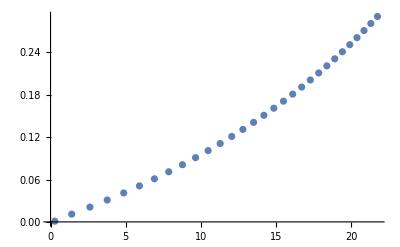

```mathematica
ListPlot[Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}]]
```

```mathematica
J=1;m=0.5;T=0.02;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list1={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list1,u1value];]
```

```mathematica
J=1;m=0.5;T=0.04;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list2={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list2,u1value];]
```

```mathematica
J=1;m=0.5;T=0.06;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list3={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list3,u1value];]
```

```mathematica
J=1;m=0.5;T=0.08;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list4={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list4,u1value];]
```

```mathematica
J=1;m=0.5;T=0.1;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list5={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list5,u1value];]
```

```mathematica
plotm05=ListPlot[{Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list1[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list2[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list3[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list4[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list5[[i]],deltalist[[i]]},{i,1,noofdelta}]},Joined->True,
Frame->True,PlotRange->{{0,22},{0,0.28}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"U_1","Δ(T)"},LabelStyle->Directive[Black,Italic,22],FrameTicks->{{{0,0.1,0.2,0.3},None},{{0,5,10,15,20},None}},
FrameStyle->Directive[Thickness[0.007]],
Epilog->{Text[Style["m=0.5",25,Italic],{4,0.25}]},
PlotLegends->Placed[LineLegend[{Style["T=0",16],Style["T=0.02",16],Style["T=0.04",16],Style["T=0.06",16],Style["T=0.08",16],Style["T=0.1",16]},LegendLayout->{"Column",1}],{1,0.6}],AspectRatio->0.7,ImageSize->500]
```

-Graphics-

```mathematica
Export["plotm05.pdf",plotm05]
```

plotm05.pdf

### example calculation: Δ-U relation and reading Tc (m=0)

```mathematica
J=1;m=0;T=0.001;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list0={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list0,u1value];]
```

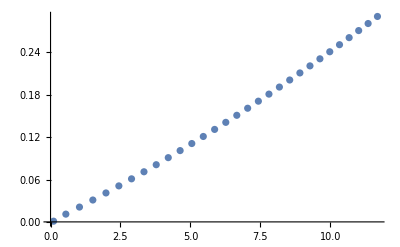

```mathematica
ListPlot[Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}]]
```

```mathematica
J=1;m=0;T=0.02;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list1={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list1,u1value];]
```

```mathematica
J=1;m=0;T=0.04;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list2={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list2,u1value];]
```

```mathematica
J=1;m=0;T=0.06;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list3={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list3,u1value];]
```

```mathematica
J=1;m=0;T=0.08;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list4={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list4,u1value];]
```

```mathematica
J=1;m=0;T=0.1;
noofdelta=30;deltastep=0.01;
deltalist=Table[ 0.001+deltastep*(i-1),{i,1,noofdelta}];
u1list5={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list5,u1value];]
```

```mathematica
plotm0=ListPlot[{Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list1[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list2[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list3[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list4[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list5[[i]],deltalist[[i]]},{i,1,noofdelta}]},Joined->True,
Frame->True,PlotRange->{{0,12},{0,0.28}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"U_1","Δ(T)"},LabelStyle->Directive[Black,22],FrameTicks->{{{0,0.1,0.2,0.3},None},{{0,5,10,15,20},None}},
FrameStyle->Directive[Thickness[0.007]],
(*Epilog->{Text[Style["m=0",25,Italic],{2,0.25}]},*)
PlotLegends->Placed[LineLegend[{Style["T=0",16],Style["T=0.02",16],Style["T=0.04",16],Style["T=0.06",16],Style["T=0.08",16],Style["T=0.1",16]},LegendLayout->{"Column",1}],{1,0.6}],AspectRatio->0.7,ImageSize->500]
```

-Graphics-

```mathematica
Export["plotm0.pdf",plotm0]
```

plotm0.pdf

### example calculation: Δ-U relation and reading Tc (m=0.1, small Δ regime)

```mathematica
J=1;m=0.1;T=0.0001;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list0={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list0,u1value];]
```

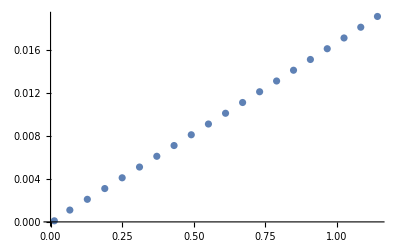

```mathematica
ListPlot[Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}]]
```

```mathematica
J=1;m=0.1;T=0.001;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list1={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list1,u1value];]
```

```mathematica
J=1;m=0.1;T=0.002;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list2={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list2,u1value];]
```

```mathematica
J=1;m=0.1;T=0.003;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list3={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list3,u1value];]
```

```mathematica
J=1;m=0.1;T=0.004;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list4={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list4,u1value];]
```

```mathematica
J=1;m=0.1;T=0.005;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list5={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list5,u1value];]
```

```mathematica
plotm01=ListPlot[{Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list1[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list2[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list3[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list4[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list5[[i]],deltalist[[i]]},{i,1,noofdelta}]},Joined->True,
Frame->True,PlotRange->{{0,0.95},{0,0.018}},
PlotStyle->Directive[Thick],Frame->True,LabelStyle->Directive[Black,22],FrameLabel->{Style["U_1",Italic,22],Style["Δ",22]},FrameTicks->{{{0,0.005,0.01,0.015,0.02},None},{{0,0.2,0.4,0.6,0.8},None}},
FrameStyle->Directive[Thickness[0.007]],
Epilog->{Text[Style["m=0.01",24,Italic],{0.8,0.002}],Text[Style["m=0",20,Italic],{0.55,0.016}]},
PlotLegends->Placed[LineLegend[{Style["T=0",16],Style["T=0.001",16],Style["T=0.002",16],Style["T=0.003",16],Style["T=0.004",16],Style["T=0.005",16]},LegendLayout->{"Column",1}],{1,0.6}],AspectRatio->0.7,ImageSize->500]
```

-Graphics-

```mathematica
Export["plotm001.pdf",plotm001]
```

plotm001.pdf

### example calculation: Δ-U relation and reading Tc (m=0.01, small Δ regime)

```mathematica
J=1;m=0.01;T=0.0001;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list0={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list0,u1value];]
```

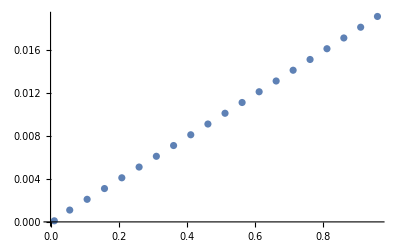

```mathematica
ListPlot[Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}]]
```

```mathematica
J=1;m=0.01;T=0.001;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list1={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list1,u1value];]
```

```mathematica
J=1;m=0.01;T=0.002;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list2={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list2,u1value];]
```

```mathematica
J=1;m=0.01;T=0.003;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list3={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list3,u1value];]
```

```mathematica
J=1;m=0.01;T=0.004;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list4={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list4,u1value];]
```

```mathematica
J=1;m=0.01;T=0.005;
noofdelta=20;deltastep=0.001;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list5={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list5,u1value];]
```

```mathematica
plotm001=ListPlot[{Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list1[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list2[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list3[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list4[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list5[[i]],deltalist[[i]]},{i,1,noofdelta}]},Joined->True,
Frame->True,PlotRange->{{0,0.95},{0,0.018}},
PlotStyle->Directive[Thick],Frame->True,LabelStyle->Directive[Black,22],FrameLabel->{Style["U_1",Italic,22],Style["Δ",22]},FrameTicks->{{{0,0.005,0.01,0.015,0.02},None},{{0,0.2,0.4,0.6,0.8},None}},
FrameStyle->Directive[Thickness[0.007]],
Epilog->{Text[Style["m=0.01",24,Italic],{0.8,0.002}],Text[Style["m=0",20,Italic],{0.55,0.016}]},
PlotLegends->Placed[LineLegend[{Style["T=0",16],Style["T=0.001",16],Style["T=0.002",16],Style["T=0.003",16],Style["T=0.004",16],Style["T=0.005",16]},LegendLayout->{"Column",1}],{1,0.6}],AspectRatio->0.7,ImageSize->500]
```

-Graphics-

```mathematica
Export["plotm001.pdf",plotm001]
```

plotm001.pdf

### example calculation: Δ-U relation and reading Tc (m=0, small Δ regime)

```mathematica
J=1;m=0;T=0.00001;
noofdelta=25;deltastep=0.0005;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list0={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list0,u1value];]
```

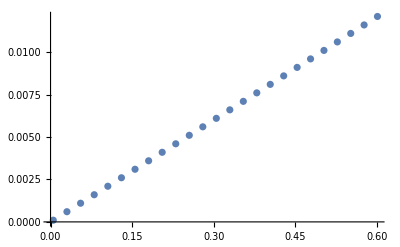

```mathematica
ListPlot[Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}]]
```

```mathematica
J=1;m=0;T=0.001;
noofdelta=25;deltastep=0.0005;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list1={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list1,u1value];]
```

```mathematica
J=1;m=0;T=0.002;
noofdelta=25;deltastep=0.0005;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list2={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list2,u1value];]
```

```mathematica
J=1;m=0;T=0.003;
noofdelta=25;deltastep=0.0005;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list3={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list3,u1value];]
```

```mathematica
J=1;m=0;T=0.004;
noofdelta=25;deltastep=0.0005;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list4={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list4,u1value];]
```

```mathematica
J=1;m=0;T=0.005;
noofdelta=25;deltastep=0.0005;
deltalist=Table[ 0.0001+deltastep*(i-1),{i,1,noofdelta}];
u1list5={};
```

```mathematica
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list5,u1value];]
```

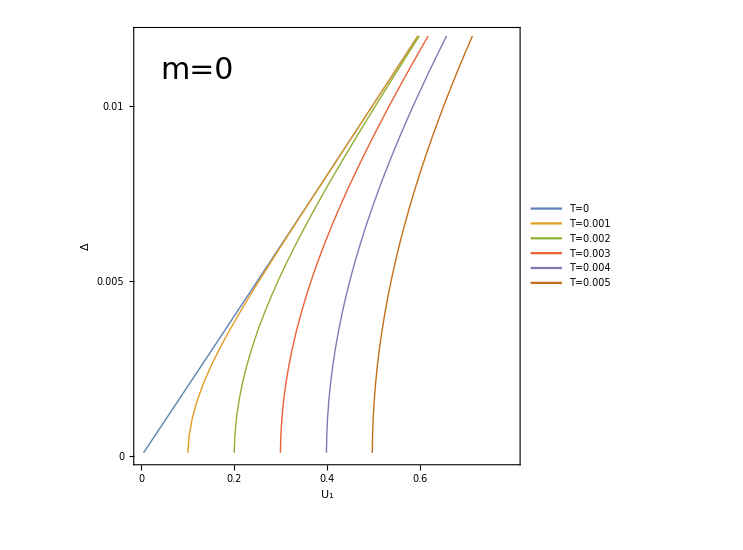

```mathematica
plotm0=ListPlot[{Table[{u1list0[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list1[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list2[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list3[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list4[[i]],deltalist[[i]]},{i,1,noofdelta}],Table[{u1list5[[i]],deltalist[[i]]},{i,1,noofdelta}]},Joined->True,
Frame->True,PlotRange->{{0,0.8},{0,0.012}},
PlotStyle->Directive[Thick],Frame->True,LabelStyle->Directive[Black,25],FrameLabel->{Style["U_1",35],Style["Δ",35]},FrameTicks->{{{0,0.005,0.01,0.015,0.02},None},{{0,0.2,0.4,0.6},None}},
FrameStyle->Directive[Thickness[0.007]],
Epilog->{Text[Style["m=0",30],{0.12,0.011}]},
PlotLegends->Placed[LineLegend[{Style["T=0",18],Style["T=0.001",18],Style["T=0.002",18],Style["T=0.003",18],Style["T=0.004",18],Style["T=0.005",18]},LegendLayout->{"Column",1}],{0.85,0.3}],AspectRatio->1,ImageSize->550]
```

```mathematica
Export["plotm0.pdf",plotm0]
```

plotm0.pdf

### delta max =0.3

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.5;
noofdelta=30;deltastep=0.01;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

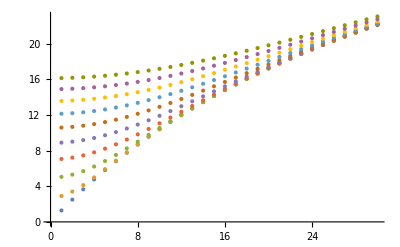

```mathematica
ListPlot[u1table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.1;
noofdelta=30;deltastep=0.01;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

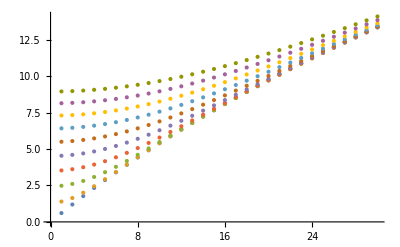

```mathematica
ListPlot[u1table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.01;
noofdelta=30;deltastep=0.01;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

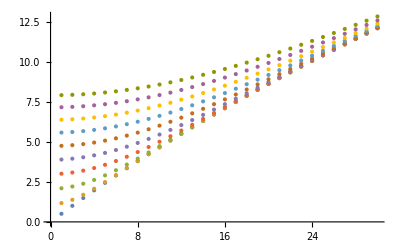

```mathematica
ListPlot[u1table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0;
noofdelta=30;deltastep=0.01;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

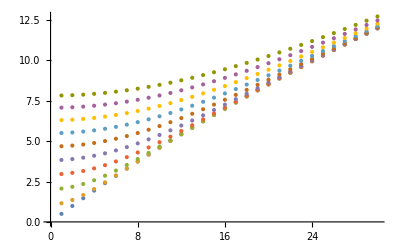

```mathematica
ListPlot[u1table]
```

### delta max =0.03

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.5;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

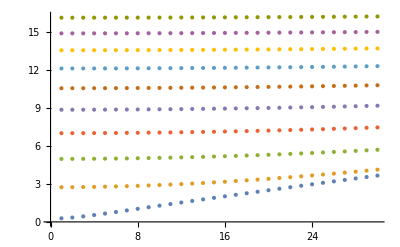

```mathematica
ListPlot[u1table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.1;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

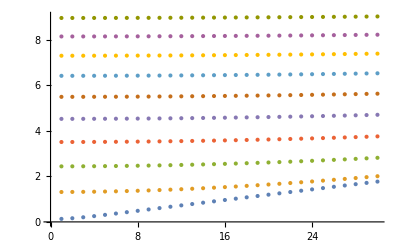

```mathematica
ListPlot[u1table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.01;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

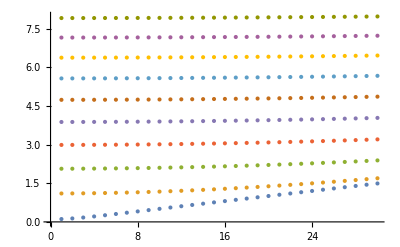

```mathematica
ListPlot[u1table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};
For[j=0,j<noofdelta,j++,integralvalue=u1integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue;AppendTo[u1list,u1value];];AppendTo[u1table,u1list]]
```

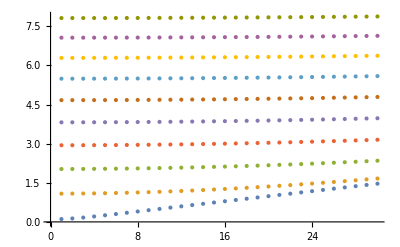

```mathematica
ListPlot[u1table]
```

### various m

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.4;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
u2table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};u2list={};
For[j=0,j<noofdelta,j++,integralvalue1=u1integral[J,m,T,deltalist[[j+1]]];
integralvalue2=u2integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue1;
u2value=1/integralvalue2;AppendTo[u1list,u1value];AppendTo[u2list,u2value];];AppendTo[u1table,u1list];
AppendTo[u2table,u2list];]
```

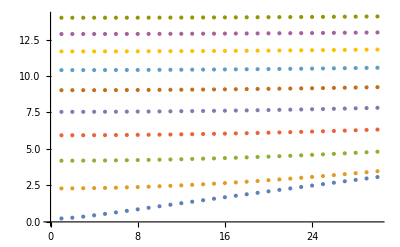

```mathematica
ListPlot[u1table]
```

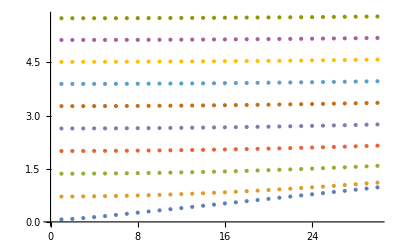

```mathematica
ListPlot[u2table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0.2;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
u2table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};u2list={};
For[j=0,j<noofdelta,j++,integralvalue1=u1integral[J,m,T,deltalist[[j+1]]];
integralvalue2=u2integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue1;
u2value=1/integralvalue2;AppendTo[u1list,u1value];AppendTo[u2list,u2value];];AppendTo[u1table,u1list];
AppendTo[u2table,u2list];]
```

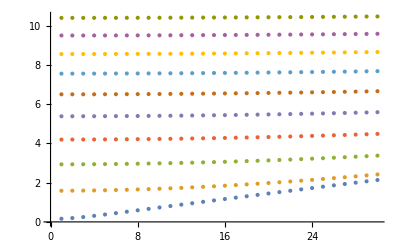

```mathematica
ListPlot[u1table]
```

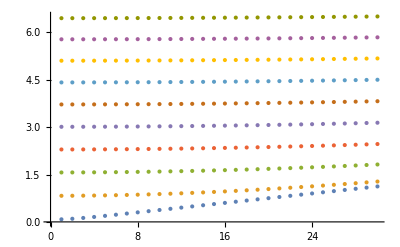

```mathematica
ListPlot[u2table]
```

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=0;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
u2table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};u2list={};
For[j=0,j<noofdelta,j++,integralvalue1=u1integral[J,m,T,deltalist[[j+1]]];
integralvalue2=u2integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue1;
u2value=1/integralvalue2;AppendTo[u1list,u1value];AppendTo[u2list,u2value];];AppendTo[u1table,u1list];
AppendTo[u2table,u2list];]
```

```mathematica
ListPlot[u1table]
```

-Graphics-

```mathematica
ListPlot[u2table]
```

-Graphics-

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=-0.2;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
u2table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};u2list={};
For[j=0,j<noofdelta,j++,integralvalue1=u1integral[J,m,T,deltalist[[j+1]]];
integralvalue2=u2integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue1;
u2value=1/integralvalue2;AppendTo[u1list,u1value];AppendTo[u2list,u2value];];AppendTo[u1table,u1list];
AppendTo[u2table,u2list];]
```

```mathematica
ListPlot[u1table]
```

-Graphics-

```mathematica
ListPlot[u2table]
```

-Graphics-

```mathematica
tlist=Table[0.001+0.01it,{it,0,9}];
J=1;m=-0.4;
noofdelta=30;deltastep=0.001;
deltalist=Table[ deltastep*idelta,{idelta,1,noofdelta}];
u1table={};
u2table={};
```

```mathematica
For[i=0,i<Length[tlist],i++,T=tlist[[i+1]];u1list={};u2list={};
For[j=0,j<noofdelta,j++,integralvalue1=u1integral[J,m,T,deltalist[[j+1]]];
integralvalue2=u2integral[J,m,T,deltalist[[j+1]]];u1value=1/integralvalue1;
u2value=1/integralvalue2;AppendTo[u1list,u1value];AppendTo[u2list,u2value];];AppendTo[u1table,u1list];
AppendTo[u2table,u2list];]
```

```mathematica
ListPlot[u1table]
```

-Graphics-

```mathematica
ListPlot[u2table]
```

## secant method to compute Δ(T)

### DEFINITION: u1tceq, u2tceq

```mathematica
u1tceq[J_?NumericQ,m_?NumericQ,temp_?NumericQ,delta_?NumericQ,u1_?NumericQ]:=u1 NIntegrate[(k/(2π))(((1-hzhat[J,m,k])/(4delta))Tanh[delta/(2temp)]+((1+hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+delta^2]))Tanh[Sqrt[edisp[J,m,k]^2+delta^2]/(2temp)]),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]-1
```

```mathematica
u2tceq[J_?NumericQ,m_?NumericQ,temp_?NumericQ,delta_?NumericQ,u2_?NumericQ]:=u2 NIntegrate[(k/(2π))(((1+hzhat[J,m,k])/(4delta))Tanh[delta/(2temp)]+((1-hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+delta^2]))Tanh[Sqrt[edisp[J,m,k]^2+delta^2]/(2temp)]),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]-1
```

### DEFINITION: secantu1step, secantu1t, secantu2step, secantu2t

the interation of single step: (for U1)

```mathematica
secantu1step[delta0_,delta1_]:=
(
input0=delta0;
input1=delta1;
inverseslope=(input1-input0)/(u1tceq[J,m,temp,input1,u1]-u1tceq[J,m,temp,input0,u1]);
output0=input1;
deltajump=inverseslope*u1tceq[J,m,temp,input1,u1];
alpha=1/(1+10 Abs[deltajump]);
output1=input1-alpha*deltajump;
)
```

full iteration: (for U1)

```mathematica
secantu1t[inputdelta_]:=
(
alpha=0.1;
output1=inputdelta;
output0=output1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.999,secantu1step[output0,output1];];
delta=output1;
)
```

the interation of single step: (for U2)

```mathematica
secantu2step[delta0_,delta1_]:=
(
input0=delta0;
input1=delta1;
inverseslope=(input1-input0)/(u2tceq[J,m,temp,input1,u2]-u2tceq[J,m,temp,input0,u2]);
output0=input1;
deltajump=inverseslope*u2tceq[J,m,temp,input1,u2];
alpha=1/(1+10 Abs[deltajump]);
output1=input1-alpha*deltajump;
)
```

full iteration: (for U2)

```mathematica
secantu2t[inputdelta_]:=
(
alpha=0.1;
output1=inputdelta;
output0=output1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.99,secantu2step[output0,output1];];
delta=output1;
)
```

#### example calculation

```mathematica
deltat0=0.01;J=1;m=0.005;
u1=1/u1integralt0[J,m,deltat0];
temp=0.002;
secantu1t[deltat0]//Timing
Print["damping factor is ",alpha]
delta
```

{0.015625,Null}

damping factor is 0.998426

0.00984263

```mathematica
deltat0=0.01;J=1;m=0.005;
u1=1/u1integralt0[J,m,deltat0];
temp=0.003;
secantu1t[deltat0]//Timing
Print["damping factor is ",alpha]
delta
```

{0.03125,Null}

damping factor is 0.989873

0.00898727

```mathematica
deltat0=0.01;J=1;m=0.005;
u1=1/u1integralt0[J,m,deltat0];
temp=0.004;
secantu1t[deltat0]//Timing
Print["damping factor is ",alpha]
delta
```

{0.03125,Null}

damping factor is 0.998562

0.0071069

```mathematica
deltat0=0.01;J=1;m=0.005;
u1=1/u1integralt0[J,m,deltat0];
temp=0.005;
secantu1t[deltat0]//Timing
Print["damping factor is ",alpha]
delta
```

{0.03125,Null}

damping factor is 0.98794

0.00221738

```mathematica
u1
```

0.502537

### plot Δ(T)--- fix delta(T=0) to be delta0

```mathematica
delta0=0.01;J=1;m=0.005;
u1=1/u1integralt0[J,m,deltat0];
templist=Table[0.0005 ioft,{ioft,1,10}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
Print[newdelta];
AppendTo[deltalist,newdelta];
]//Timing
u1
```

0.01

0.009999

0.00997172

0.00984555

0.0095521

0.00903918

0.00824966

0.00709305

0.00538359

0.00166369

{0.1875,Null}

0.502537

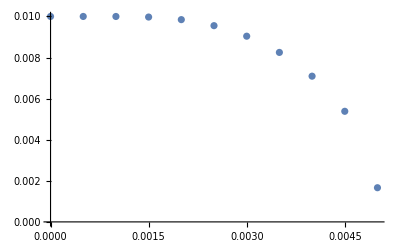

```mathematica
tempdata={0}~Join~templist;
deltadata={delta0}~Join~deltalist;
ListPlot[Table[{tempdata[[j]],deltadata[[j]]},{j,1,Length[tempdata]}]]
```

```mathematica
delta0=0.01;J=1;m=0.3;
u1=1/u1integralt0[J,m,deltat0];
templist=Table[0.0005 ioft,{ioft,1,10}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
Print[newdelta];
AppendTo[deltalist,newdelta];
]//Timing
u1
```

0.01

0.009999

0.00997172

0.00984555

0.0095521

0.00903919

0.00824969

0.00709311

0.00538371

0.0016642

{0.1875,Null}

0.890029

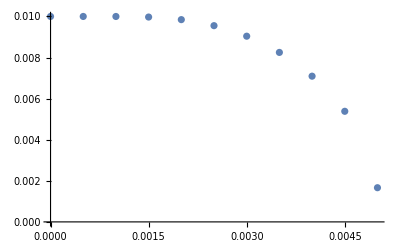

```mathematica
tempdata={0}~Join~templist;
deltadata={delta0}~Join~deltalist;
ListPlot[Table[{tempdata[[j]],deltadata[[j]]},{j,1,Length[tempdata]}]]
```

### Δ(T) plot: fix Δ(T=0)=0.2, compare solution of gap1 and gap2***

```mathematica
(*Δ=0.5, m=0.2*)
```

```mathematica
delta0=0.5;J=1;m=0.2;ecutoff=2;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
```

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,131}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data05gap1=Table[{templist[[j]]/ecutoff,deltalist[[j]]/ecutoff},{j,1,Length[deltalist]}];
```

{0.140625,Null}

u1 value:21.3876u2 value:16.1653

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,127}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data05gap2=Table[{templist[[j]]/ecutoff,deltalist[[j]]/ecutoff},{j,1,Length[deltalist]}];
```

{0.140625,Null}

u1 value:21.3876u2 value:16.1653

```mathematica
(*Δ=0.2, m=0.2*)
```

```mathematica
delta0=0.2;J=1;m=0.2;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
```

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data02gap1=Table[{templist[[j]]/ecutoff,deltalist[[j]]/ecutoff},{j,1,Length[deltalist]}];
```

{0.109375,Null}

u1 value:11.2292u2 value:7.05394

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data02gap2=Table[{templist[[j]]/ecutoff,deltalist[[j]]/ecutoff},{j,1,Length[deltalist]}];
```

{0.25,Null}

u1 value:11.2292u2 value:7.05394

```mathematica
OverTilde[Δ]
```

Δ̃

```mathematica
twogapplot=ListPlot[{data05gap1,data05gap2,data02gap1,data02gap2},Joined->True,
PlotStyle->{{Thick,RGBColor[1,0.5,0]},{Thick,RGBColor[1,0.5,0],Dashed},{Thick,RGBColor[0,0.5,1]},{Thick,RGBColor[0,0.5,1],Dashed}},
PlotRange->{{0,0.15},{0,0.26}},
Frame->True,FrameLabel->{{"(Δ̃)_α(T)/ε_Λ",None},{"T/ε_Λ",None}},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25},None},{{0,0.05,0.1,0.15},None}},
LabelStyle->Directive[Black, 20],
Epilog->{(*Text[Style["m=0.2",23],{0.23,0.47}],*)Text[Style["T_MF",20],{0.115,0.02}],Text[Style["T_MF",20],{0.04,0.02}]},
PlotLegends->Placed[{Style["(Δ̃)_1(T) for Δ(0)=0.25ε_Λ",20],Style["(Δ̃)_2(T) for Δ(0)=0.25ε_Λ",20],Style["(Δ̃)_1(T) for Δ(0)=0.1ε_Λ",20],Style["(Δ̃)_2(T) for Δ(0)=0.1ε_Λ",20]},{1,0.6}],
ImageSize->600,AspectRatio->0.7]
```

-Graphics-

```mathematica
Export["twogap.pdf",twogapplot]
```

twogap.pdf

### Δ(T) plot: fix Δ(T=0)=0, compare solution of gap1 and gap2(*)

```mathematica
(*Δ=0.5, m=0.2*)
```

```mathematica
delta0=0.5;J=1;m=0.2;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
```

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,131}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data05gap1=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[deltalist]}];
```

{3.96875,Null}

u1 value:21.3876u2 value:16.1653

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,127}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data05gap2=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[deltalist]}];
```

{2.89063,Null}

u1 value:21.3876u2 value:16.1653

```mathematica
(*Δ=0.2, m=0.2*)
```

```mathematica
delta0=0.2;J=1;m=0.2;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
```

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data02gap1=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[deltalist]}];
```

{1.5,Null}

u1 value:11.2292u2 value:7.05394

```mathematica
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
data02gap2=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[deltalist]}];
```

{1.20313,Null}

u1 value:11.2292u2 value:7.05394

```mathematica
twogapplot=ListPlot[{data05gap1,data05gap2,data02gap1,data02gap2},Joined->True,
PlotStyle->{{Thick,RGBColor[1,0.5,0]},{Thick,RGBColor[1,0.5,0],Dashed},{Thick,RGBColor[0,0.5,1]},{Thick,RGBColor[0,0.5,1],Dashed}},
PlotRange->{{0,0.27},{0,0.52}},
Frame->True,FrameLabel->{{"Δ(T)",None},{"T",None}},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4,0.5},None},{{0,0.05,0.10,0.15,0.20,0.25},None}},
LabelStyle->Directive[Black, 20],
Epilog->{Text[Style["m=0.2",23],{0.23,0.47}],Text[Style["T_c",20],{0.235,0.04}],Text[Style["T_c",20],{0.08,0.04}]},
PlotLegends->Placed[{Style["Δ(0)=0.5, α=1",20],Style["Δ(0)=0.5, α=2",20],Style["Δ(0)=0.2, α=1",20],Style["Δ(0)=0.2, α=2",20]},{1,0.6}],
ImageSize->600,AspectRatio->0.7]
```

-Graphics-

```mathematica
Export["twogap.pdf",twogapplot]
```

twogap.pdf

### plot Δ(T)--- fix U_1 and delta0 serves as trial

```mathematica
u1=1;J=1;m=0;
delta0=0.021;
templist=Table[0.0002 ioft+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.5625,Null}

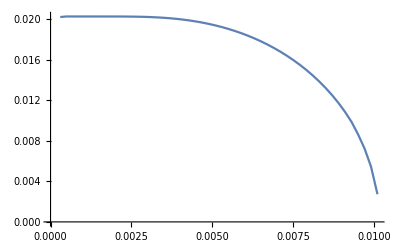

```mathematica
data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]
```

```mathematica
u1=1;J=1;m=0.01;
delta0=0.02;
templist=Table[0.0002 ioft+0.0001,{ioft,1,49}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.796875,Null}

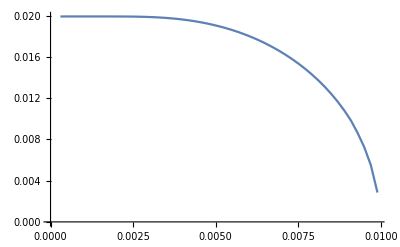

```mathematica
data01=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data01,Joined->True]
```

```mathematica
u1=1;J=1;m=0.02;
delta0=0.02;
templist=Table[0.0002 ioft+0.0001,{ioft,1,48}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.6875,Null}

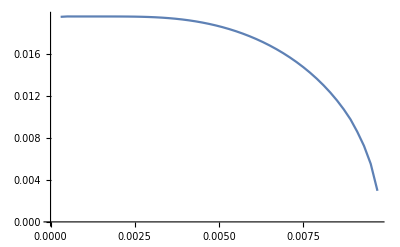

```mathematica
data02=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data02,Joined->True]
```

```mathematica
u1=1;J=1;m=0.03;
delta0=0.02;
templist=Table[0.0002 ioft+0.0001,{ioft,1,48}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{1.1875,Null}

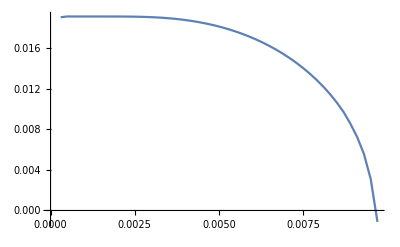

```mathematica
data03=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data03,Joined->True]
```

```mathematica
u1=1;J=1;m=0.04;
delta0=0.018;
templist=Table[0.0002 ioft+0.0001,{ioft,1,47}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.75,Null}

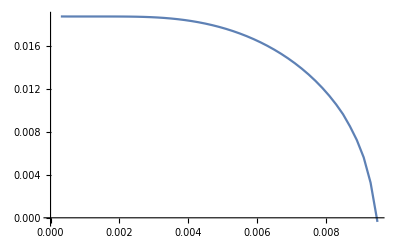

```mathematica
data04=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data04,Joined->True]
```

```mathematica
u1=1;J=1;m=0.05;
delta0=0.017;
templist=Table[0.0002 ioft+0.0001,{ioft,1,46}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{2.32813,Null}

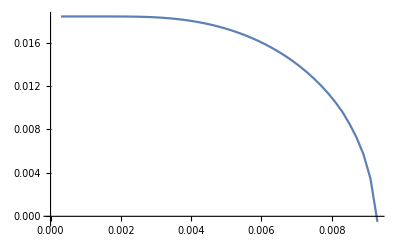

```mathematica
data05=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data05,Joined->True]
```

```mathematica
u1=1;J=1;m=0.1;
delta0=0.016;
templist=Table[0.0002 ioft+0.0001,{ioft,1,41}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.59375,Null}

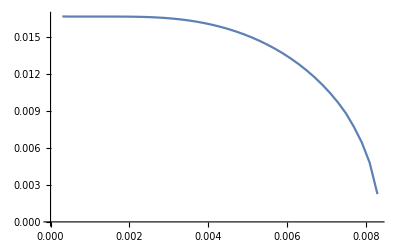

```mathematica
data1=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data1,Joined->True]
```

```mathematica
u1=1;J=1;m=0.2;
delta0=0.014;
templist=Table[0.0002 ioft+0.0001,{ioft,1,34}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.59375,Null}

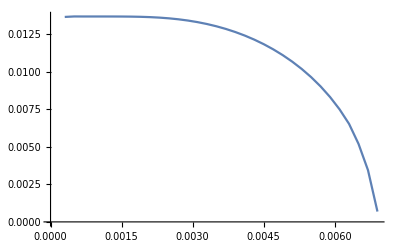

```mathematica
data2=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data2,Joined->True]
```

```mathematica
u1=1;J=1;m=0.3;
delta0=0.011;
templist=Table[0.0002 ioft+0.0001,{ioft,1,28}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.453125,Null}

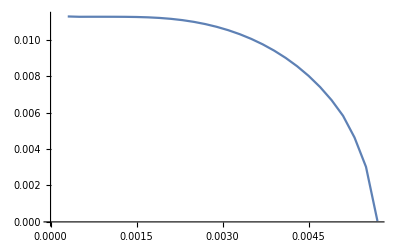

```mathematica
data3=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data3,Joined->True]
```

```mathematica
u1=1;J=1;m=-0.01;
delta0=0.022;
templist=Table[0.0002 ioft+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.765625,Null}

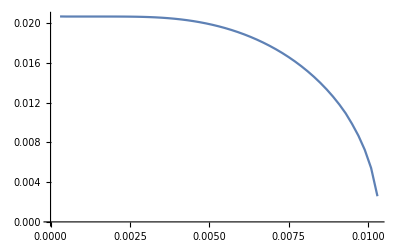

```mathematica
data01n=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data01n,Joined->True]
```

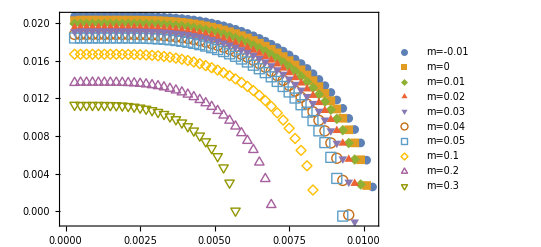

```mathematica
ListPlot[{data01n,data00,data01,data02,data03,data04,data05,data1,data2,data3},PlotMarkers->Automatic,PlotLegends->{"m=-0.01","m=0","m=0.01","m=0.02","m=0.03","m=0.04","m=0.05","m=0.1","m=0.2","m=0.3"},Frame->True,LabelStyle->Directive[Black, 15]]
```

### plot Δ(T)--- fix U_2 and delta0 serves as trial

```mathematica
u2=1;J=1;m=0;
delta0=0.021;
templist=Table[0.0002 ioft+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.734375,Null}

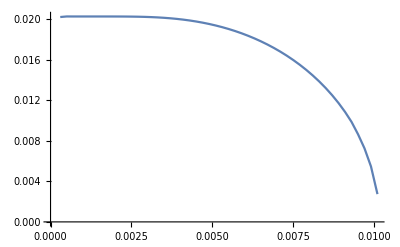

```mathematica
data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]
```

```mathematica
u2=1;J=1;m=0.01;
delta0=0.02;
templist=Table[0.0002 ioft+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.765625,Null}

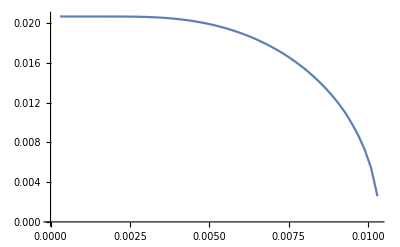

```mathematica
data01=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data01,Joined->True]
```

```mathematica
u2=1;J=1;m=0.02;
delta0=0.02;
templist=Table[0.0002 ioft+0.0001,{ioft,1,52}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{1.09375,Null}

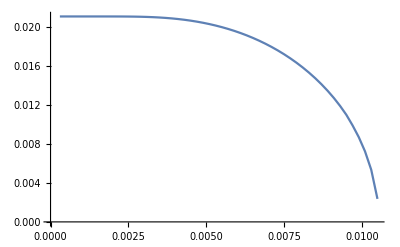

```mathematica
data02=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data02,Joined->True]
```

```mathematica
u2=1;J=1;m=0.03;
delta0=0.02;
templist=Table[0.0002 ioft+0.0001,{ioft,1,53}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{1.04688,Null}

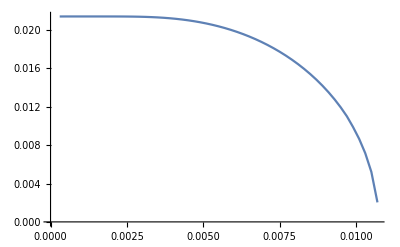

```mathematica
data03=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data03,Joined->True]
```

```mathematica
u2=1;J=1;m=0.04;
delta0=0.022;
templist=Table[0.0002 ioft+0.0001,{ioft,1,54}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.796875,Null}

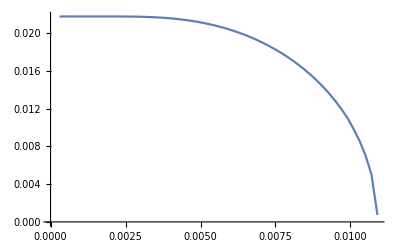

```mathematica
data04=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data04,Joined->True]
```

```mathematica
u2=1;J=1;m=0.05;
delta0=0.022;
templist=Table[0.0002 ioft+0.0001,{ioft,1,55}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.84375,Null}

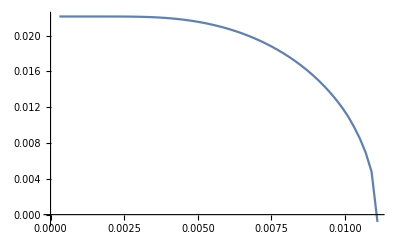

```mathematica
data05=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data05,Joined->True]
```

```mathematica
u2=1;J=1;m=0.1;
delta0=0.022;
templist=Table[0.0002 ioft+0.0001,{ioft,1,59}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.859375,Null}

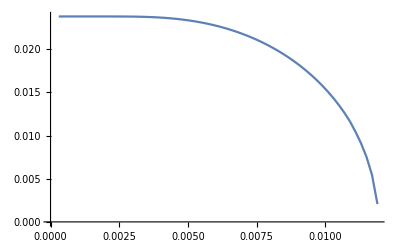

```mathematica
data1=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data1,Joined->True]
```

```mathematica
u2=1;J=1;m=0.2;
delta0=0.027;
templist=Table[0.0002 ioft+0.0001,{ioft,1,66}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.921875,Null}

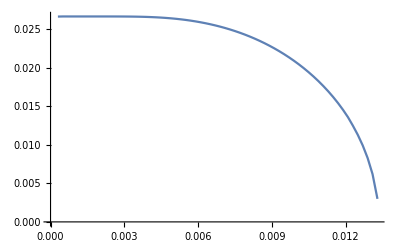

```mathematica
data2=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data2,Joined->True]
```

```mathematica
u2=1;J=1;m=0.3;
delta0=0.027;
templist=Table[0.0002 ioft+0.0001,{ioft,1,72}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{1.04688,Null}

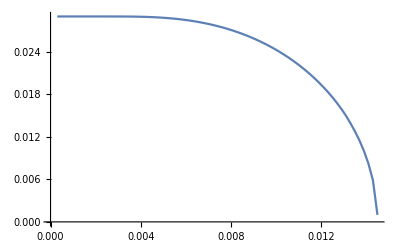

```mathematica
data3=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data3,Joined->True]
```

```mathematica
u2=1;J=1;m=-0.01;
delta0=0.022;
templist=Table[0.0002 ioft+0.0001,{ioft,1,49}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.671875,Null}

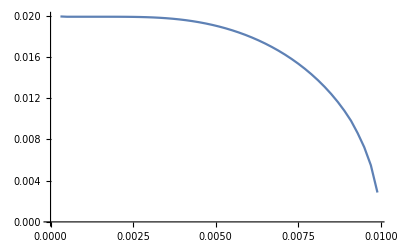

```mathematica
data01n=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data01n,Joined->True]
```

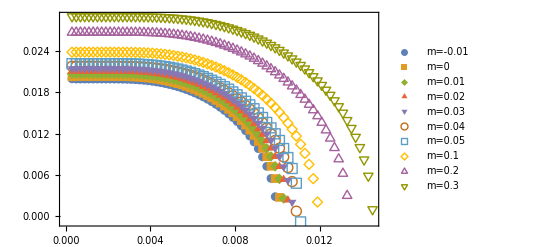

```mathematica
ListPlot[{data01n,data00,data01,data02,data03,data04,data05,data1,data2,data3},PlotMarkers->Automatic,PlotLegends->{"m=-0.01","m=0","m=0.01","m=0.02","m=0.03","m=0.04","m=0.05","m=0.1","m=0.2","m=0.3"},Frame->True,LabelStyle->Directive[Black, 15]]
```

## finite temperature D_s calculation

### DEFINITION:

```mathematica
(*the x direction has been averaged*)
vsquare[J_,m_,k_]:=2J^2k^(4J-2)/(m^2+k^(2J))
```

```mathematica
(* QM of the band*)
gvxx[J_,m_,k_]:=J^2 k^(2J-2)(m^2+k^(2J)/2)/(4(m^2+k^(2J))^2)
```

```mathematica
quasidisp[J_,m_,k_,deltat_]:=Sqrt[edisp[J,m,k]^2+deltat^2]
```

```mathematica
(*total Ds integral*)
dsconv[J_?NumericQ,m_?NumericQ,deltat_?NumericQ,temp_?NumericQ]:=NIntegrate[(k/(2π))(deltat^2/quasidisp[J,m,k,deltat]^3)(Tanh[quasidisp[J,m,k,deltat]/(2temp)]-(quasidisp[J,m,k,deltat]/(2temp))Sech[quasidisp[J,m,k,deltat]/(2temp)]^2)vsquare[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
dsgeo[J_?NumericQ,m_?NumericQ,deltat_?NumericQ,temp_?NumericQ]:=NIntegrate[(k/(2π))4deltat^2(Tanh[deltat/(2temp)]/deltat-Tanh[quasidisp[J,m,k,deltat]/(2temp)]/quasidisp[J,m,k,deltat])gvxx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
f[λ_]:=1-λ^2-2Log[λ]
```

```mathematica
f[0.1]
```

5.59517

```mathematica
f[0.01]
```

10.2102

```mathematica
(*total Ds integral*)
dsconvzerot[J_?NumericQ,m_?NumericQ,deltat_?NumericQ]:=NIntegrate[(k/(2π))(deltat^2/quasidisp[J,m,k,deltat]^3)vsquare[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
dsgeozerot[J_?NumericQ,m_?NumericQ,deltat_?NumericQ]:=NIntegrate[(k/(2π))4deltat^2(1/deltat-1/quasidisp[J,m,k,deltat])gvxx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### D_s(T) plot: fix Δ(T=0)=0.01

```mathematica
(*m=0.1*)
```

```mathematica
delta0=0.01;J=1;m=0.1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.921875,Null}

u1 value:0.605347u2 value:0.423203

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=0.01*)
```

```mathematica
delta0=0.01;J=1;m=0.01;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.953125,Null}

u1 value:0.507454u2 value:0.488377

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data001=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=0*)
```

```mathematica
delta0=0.01;J=1;m=0;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.78125,Null}

u1 value:0.497703u2 value:0.497703

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=-0.01*)
```

```mathematica
delta0=0.01;J=1;m=-0.01;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{1.,Null}

u1 value:0.488377u2 value:0.507454

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
datam001=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*plot dashed part and solid part*)
```

```mathematica
data0first=Table[data0[[j]],{j,1,34}];
data0second=Table[data0[[j]],{j,35,Length[templist]}];
data001first=Table[data001[[j]],{j,1,32}];
data001second=Table[data001[[j]],{j,33,Length[templist]}];
data003first=Table[data003[[j]],{j,1,28}];
data003second=Table[data003[[j]],{j,29,Length[templist]}];
data01first=Table[data01[[j]],{j,1,22}];
data01second=Table[data01[[j]],{j,23,Length[templist]}];
datam001first=Table[datam001[[j]],{j,1,32}];
datam001second=Table[datam001[[j]],{j,33,Length[templist]}];
```

```mathematica
line=Table[{templist[[j]],templist[[j]]},{j,1,35}];
tbktniceplot=ListPlot[{data0first,data001first,data003first,data01first,datam001first,line,data0second,data001second,data003second,data01second,datam001second},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Red},{Thick,Yellow},{Thick,Black},{Thick,Blue,Dashed},{Thick,Orange,Dashed},{Thick,Green,Dashed},{Thick,Red,Dashed},{Thick,Yellow,Dashed}},PlotRange->{{0,0.005},{0,0.005}},
Frame->True,FrameLabel->{{"D_s",None},{"T",None}},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0,0.001,0.002,0.003,0.004},None},{{0,0.001,0.002,0.003,0.004,0.005},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[{Style["m=0",20],Style["m=0.01",20],Style["m=0.032",20],Style["m=0.1",20],Style["m=-0.01",20]},{1,0.6}],
Epilog->{Text[Style["T_c^*",20],{0.00435,0.0003}],Dashed,Line[{{0.0021,0},{0.0021,0.0021}}],Text[Style["T_BKT",20],{0.0017,0.0003}]},
ImageSize->600,AspectRatio->0.7
]
```

-Graphics-

```mathematica
line=Table[{templist[[j]],templist[[j]]},{j,1,35}];
tbktniceplot=ListPlot[{data0first,data001first,data01first,line,data0second,data001second,data01second},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Black},{Thick,Blue,Dashing[{0.03,0.03}]},{Thick,Orange,Dashing[{0.03,0.03}]},{Thick,Green,Dashing[{0.03,0.03}]}},PlotRange->{{0,0.005},{0,0.005}},
Frame->True,FrameLabel->{Style["T",25],Style["D_s^tot",25]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0,0.001,0.002,0.003,0.004},None},{{0,0.001,0.002,0.003,0.004,0.005},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[{Style["m=0",20],Style["m=0.01",20],Style["m=0.1",20]},{1,0.6}],
Epilog->{Text[Style["T_c^*",20],{0.00435,0.0003}],Dashed,Thick,Line[{{0.0021,0},{0.0021,0.0021}}],Text[Style["T_BKT",20],{0.0017,0.0003}]},
AspectRatio->0.7,ImageSize->600
]
```

-Graphics-

```mathematica
Export["tbktnice.pdf",tbktniceplot]
```

tbktnice.pdf

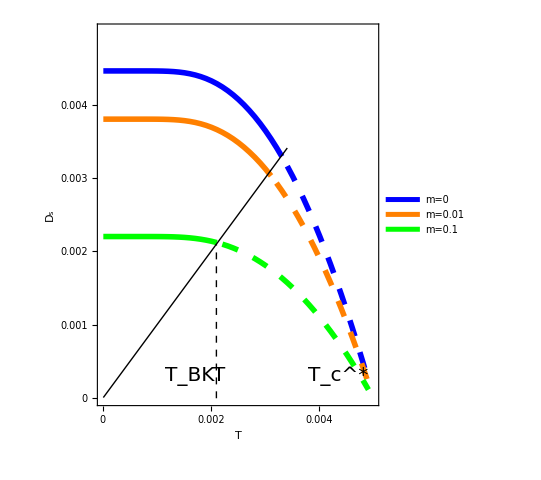

```mathematica
line=Table[{templist[[j]],templist[[j]]},{j,1,35}];
tbktniceplot1=ListPlot[{data0first,data001first,(*data003first,*)data01first,line,data0second,data001second,(*data003second,*)data01second},Joined->True,
PlotStyle->{{Thick,Blue,Thickness[0.01]},{Thick,Orange,Thickness[0.01]},{Thick,Green,Thickness[0.01]},(*{Thick,Red},*){Thick,Black},{Thick,Blue,Thickness[0.01],Dashing[{0.03,0.03}]},{Thick,Orange,Thickness[0.01],Dashing[{0.03,0.03}]},{Thick,Green,Thickness[0.01],Dashing[{0.03,0.03}]}(*,{Thick,Red,Dashed}*)},PlotRange->{{0,0.005},{0,0.005}},
Frame->True,FrameLabel->{Style["T",25],Style["D_s",25]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0,0.001,0.002,0.003,0.004},None},{{0,0.001,0.002,0.003,0.004,0.005},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[{Style["m=0",20],Style["m=0.01",20],(*Style["m=0.032",20],*)Style["m=0.1",20]},{0.82,0.85}],
Epilog->{Text[Style["T_c^*",20],{0.00435,0.0003}],Dashed,Thick,Line[{{0.0021,0},{0.0021,0.0021}}],Text[Style["T_BKT",20],{0.0017,0.0003}]},
AspectRatio->1.2,ImageSize->400
]
```

```mathematica
Export["tbktnice.pdf",tbktniceplot1]
```

tbktnice.pdf

### D_s(T) plot: fix Δ(T=0)=0.1 *

```mathematica
(*m=1*)
```

```mathematica
delta0=0.2;J=1;m=1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002(ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.28125,Null}

u1 value:31.1058u2 value:5.45797

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data1=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0.1*)
```

```mathematica
delta0=0.2;J=1;m=0.1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.,Null}

u1 value:9.71178u2 value:7.66086

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0*)
```

```mathematica
delta0=0.2;J=1;m=0;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.046875,Null}

u1 value:8.51238u2 value:8.51238

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*plot dashed part and solid part*)
```

```mathematica
data0first=Table[data0[[j]],{j,1,11}];
data0second=Table[data0[[j]],{j,12,Length[templist]}];
data01first=Table[data01[[j]],{j,1,8}];
data01second=Table[data01[[j]],{j,9,Length[templist]}];
data1first=Table[data1[[j]],{j,1,2}];
data1second=Table[data1[[j]],{j,3,Length[templist]}];
```

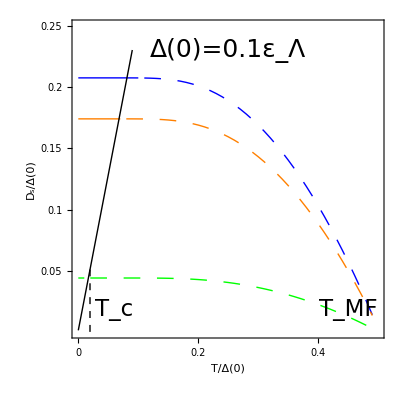

```mathematica
line=Table[{templist[[j]]/delta0,(8/π)templist[[j]]/delta0},{j,1,10}];
tbktniceplotlarge=ListPlot[{data0first,data01first,data1first,line,data0second,data01second,data1second},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Black},{Thick,Blue,Dashing[{0.03,0.03}]},{Thick,Orange,Dashing[{0.03,0.03}]},{Thick,Green,Dashing[{0.03,0.03}]}},PlotRange->{{0,0.5},{0,0.25}},
Frame->True,FrameLabel->{Style["T/Δ(0)",28],Style["D_s/Δ(0)",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25},None},{{0,0.1,0.2,0.3,0.4,0.5},None}},
LabelStyle->Directive[Black, 25],
(*PlotLegends->Placed[LineLegend[{Style["m=0",23],Style["m=Δ(0)",23],Style["m=10Δ(0)",23]},LegendLayout->"Column"],{0.775,0.84}],*)
Epilog->{Text[Style["T_MF",23],{0.45,0.018}],Dashed,Thick,Line[{{0.02,0},{0.02,0.02(8/π)}}],Text[Style["T_c",23],{0.06,0.018}],Text[Style["Δ(0)=0.1ε_Λ",25],{0.25,0.23}]},
AspectRatio->1,ImageSize->400
]
```

```mathematica
Export["tbktnicelarge.pdf",tbktniceplotlarge]
```

tbktnicelarge.pdf

### D_s(T) plot: fix Δ(T=0)=0.01 *

```mathematica
(*m=0.1*)
```

```mathematica
delta0=0.02;J=1;m=0.1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0002 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.,Null}

u1 value:1.19438u2 value:0.841631

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0.01*)
```

```mathematica
delta0=0.02;J=1;m=0.01;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0002 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.015625,Null}

u1 value:1.0045u2 value:0.967913

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data001=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0*)
```

```mathematica
delta0=0.02;J=1;m=0;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0002 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.015625,Null}

u1 value:0.98579u2 value:0.98579

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*plot dashed part and solid part*)
```

```mathematica
data0first=Table[data0[[j]],{j,1,18}];
data0second=Table[data0[[j]],{j,19,Length[templist]}];
data001first=Table[data001[[j]],{j,1,15}];
data001second=Table[data001[[j]],{j,16,Length[templist]}];
data01first=Table[data01[[j]],{j,1,9}];
data01second=Table[data01[[j]],{j,10,Length[templist]}];
```

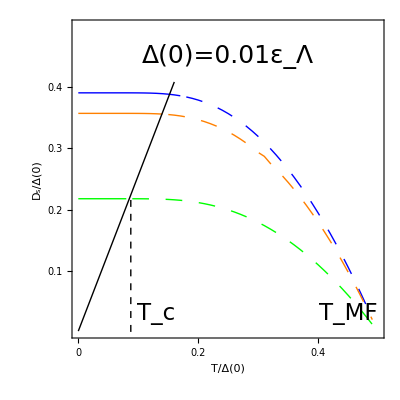

```mathematica
line=Table[{templist[[j]]/delta0,(8/π)templist[[j]]/delta0},{j,1,17}];
tbktniceplotsmall=ListPlot[{data0first,data001first,data01first,line,data0second,data001second,data01second},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Black},{Thick,Blue,Dashing[{0.03,0.03}]},{Thick,Orange,Dashing[{0.03,0.03}]},{Thick,Green,Dashing[{0.03,0.03}]}},PlotRange->{{0,0.5},{0,0.5}},
Frame->True,FrameLabel->{Style["T/Δ(0)",28],Style["D_s/Δ(0)",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0,0.1,0.2,0.3,0.4,0.5},None}},
LabelStyle->Directive[Black, 25],
(*PlotLegends->Placed[LineLegend[{Style["m=0",23],Style["m=Δ(0)",23],Style["m=10Δ(0)",23]},LegendLayout->"Column"],{0.775,0.84}],*)
Epilog->{Text[Style["T_MF",23],{0.45,0.03}],Dashed,Thick,Line[{{0.088,0},{0.088,0.088(8/π)}}],Text[Style["T_c",23],{0.13,0.03}],Text[Style["Δ(0)=0.01ε_Λ",25],{0.25,0.45}]},
AspectRatio->1,ImageSize->400
]
```

```mathematica
Export["tbktnicesmall.pdf",tbktniceplotsmall]
```

tbktnicesmall.pdf

### D_s(T) plot: fix Δ(T=0)=0.1 (fix m/cutoff ratio)***

```mathematica
(*m=1*)
```

```mathematica
delta0=0.2;J=1;m=1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002(ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.140625,Null}

u1 value:31.1058u2 value:5.45797

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data1=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0.1*)
```

```mathematica
delta0=0.2;J=1;m=0.1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.,Null}

u1 value:9.71178u2 value:7.66086

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0*)
```

```mathematica
delta0=0.2;J=1;m=0;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.,Null}

u1 value:8.51238u2 value:8.51238

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*plot dashed part and solid part*)
```

```mathematica
data0first=Table[data0[[j]],{j,1,11}];
data0second=Table[data0[[j]],{j,12,Length[templist]}];
data01first=Table[data01[[j]],{j,1,8}];
data01second=Table[data01[[j]],{j,9,Length[templist]}];
data1first=Table[data1[[j]],{j,1,2}];
data1second=Table[data1[[j]],{j,3,Length[templist]}];
```

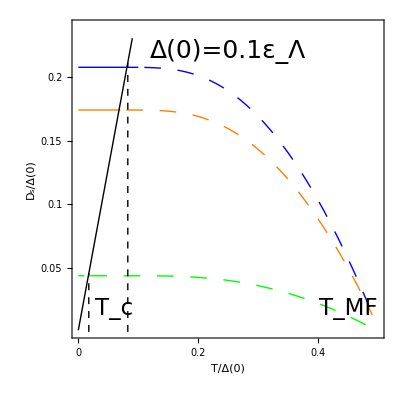

```mathematica
line=Table[{templist[[j]]/delta0,(8/π)templist[[j]]/delta0},{j,1,10}];
tbktniceplotlarge=ListPlot[{data0first,data01first,data1first,line,data0second,data01second,data1second},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Black},{Thick,Blue,Dashing[{0.03,0.03}]},{Thick,Orange,Dashing[{0.03,0.03}]},{Thick,Green,Dashing[{0.03,0.03}]}},PlotRange->{{0,0.5},{0,0.24}},
Frame->True,FrameLabel->{Style["T/Δ(0)",28],Style["D_s/Δ(0)",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2},None},{{0,0.1,0.2,0.3,0.4,0.5},None}},
LabelStyle->Directive[Black, 25],
(*PlotLegends->Placed[LineLegend[{Style["m=0",23],Style["m=Δ(0)",23],Style["m=10Δ(0)",23]},LegendLayout->"Column"],{0.775,0.84}],*)
Epilog->{Text[Style["T_MF",23],{0.45,0.018}],Dashed,Thick,Line[{{0.018,0},{0.018,0.018(8/π)}}],Line[{{0.083,0},{0.083,0.083(8/π)}}],Text[Style["T_c",23],{0.06,0.018}],Text[Style["Δ(0)=0.1ε_Λ",25],{0.25,0.22}]},
AspectRatio->1,ImageSize->400
]
```

```mathematica
Export["tbktnicelarge.pdf",tbktniceplotlarge]
```

tbktnicelarge.pdf

### D_s(T) plot: fix Δ(T=0)=0.01 (fix m/cutoff ratio)***

```mathematica
(*m=1*)
```

```mathematica
delta0=0.02;J=1;m=1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0002 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.390625,Null}

u1 value:5.38209u2 value:0.549416

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0.01*)
```

```mathematica
delta0=0.02;J=1;m=0.01;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0002 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.3125,Null}

u1 value:1.0045u2 value:0.967913

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data001=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*m=0*)
```

```mathematica
delta0=0.02;J=1;m=0;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.0002 (ioft-1)+0.00001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{0.3125,Null}

u1 value:0.98579u2 value:0.98579

```mathematica
(*data00=Table[{templist[[j]],deltalist[[j]]},{j,1,Length[templist]}];
ListPlot[data00,Joined->True]*)
```

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]]/delta0,(dsgeolist[[j]]+dsconvlist[[j]])/delta0},{j,1,Length[templist]}];
```

```mathematica
(*plot dashed part and solid part*)
```

```mathematica
data0first=Table[data0[[j]],{j,1,18}];
data0second=Table[data0[[j]],{j,19,Length[templist]}];
data001first=Table[data001[[j]],{j,1,15}];
data001second=Table[data001[[j]],{j,16,Length[templist]}];
data01first=Table[data01[[j]],{j,1,9}];
data01second=Table[data01[[j]],{j,10,Length[templist]}];
```

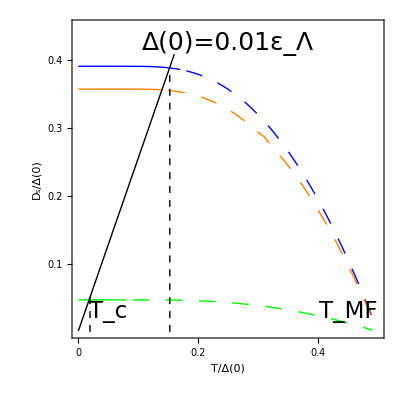

```mathematica
line=Table[{templist[[j]]/delta0,(8/π)templist[[j]]/delta0},{j,1,17}];
tbktniceplotsmall=ListPlot[{data0first,data001first,data01first,line,data0second,data001second,data01second},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Black},{Thick,Blue,Dashing[{0.03,0.03}]},{Thick,Orange,Dashing[{0.03,0.03}]},{Thick,Green,Dashing[{0.03,0.03}]}},PlotRange->{{0,0.5},{0,0.45}},
Frame->True,FrameLabel->{Style["T/Δ(0)",28],Style["D_s/Δ(0)",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0,0.1,0.2,0.3,0.4,0.5},None}},
LabelStyle->Directive[Black, 25],
(*PlotLegends->Placed[LineLegend[{Style["m=0",23],Style["m=Δ(0)",23],Style["m=10Δ(0)",23]},LegendLayout->"Column"],{0.775,0.84}],*)
Epilog->{Text[Style["T_MF",23],{0.45,0.03}],Dashed,Thick,Line[{{0.02,0},{0.02,0.02(8/π)}}],Line[{{0.153,0},{0.153,0.153(8/π)}}],Text[Style["T_c",23],{0.05,0.03}],Text[Style["Δ(0)=0.01ε_Λ",25],{0.25,0.425}]},
AspectRatio->1,ImageSize->400
]
```

```mathematica
Export["tbktnicesmall.pdf",tbktniceplotsmall]
```

tbktnicesmall.pdf

### D_s(T) plot: fix Δ(T=0)=0.2, use gap of U2

```mathematica
(*m=0*)
```

```mathematica
delta0=0.2;J=1;m=0;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{1.,Null}

u1 value:8.51238u2 value:8.51238

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=0.1*)
```

```mathematica
delta0=0.2;J=1;m=0.1;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{1.35938,Null}

u1 value:9.71178u2 value:7.66086

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=0.5*)
```

```mathematica
delta0=0.2;J=1;m=0.5;
u1=1/u1integralt0[J,m,delta0];
u2=1/u2integralt0[J,m,delta0];
templist=Table[0.002 (ioft-1)+0.0001,{ioft,1,50}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu2t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
Print["u1 value:", u1,"u2 value:",u2]
```

{1.28125,Null}

u1 value:17.2092u2 value:6.05292

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data05=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
line=Table[{templist[[j]],templist[[j]]},{j,1,35}];
tbktniceplot=ListPlot[{data0,data01,data05},Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green}},PlotRange->{{0,0.105},{0,0.05}},
Frame->True,FrameLabel->{{"D_s",None},{"T",None}},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0,0.001,0.002,0.003,0.004},None},{{0,0.001,0.002,0.003,0.004,0.005},None}},*)
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[{Style["m=0",20],Style["m=0.1",20],Style["m=0.5",20]},{1,0.6}],
ImageSize->600,AspectRatio->0.7
]
```

-Graphics-

### analytical check

```mathematica
J=1;m=0.1;
delta=0.3;T=0.03;
integral1=NIntegrate[(1/edisp[J,m,k])Tanh[edisp[J,m,k]/(2T)]k,{k,0,1}]
```

0.452475

```mathematica
integral2=NIntegrate[(1/Sqrt[delta^2+edisp[J,m,k]^2])k,{k,0,1}]
```

0.417921

```mathematica
J=1;m=-5;
delta=0.3;T=0.03;
integral1=NIntegrate[(1/edisp[J,m,k])Tanh[edisp[J,m,k]/(2T)]k,{k,0,1}]
```

0.0495098

```mathematica
integral2=NIntegrate[(1/Sqrt[delta^2+edisp[J,m,k]^2])k,{k,0,1}]
```

0.0494879

```mathematica
J=1;m=0;
delta=0.02;T=0.01;
integral1=NIntegrate[(1/edisp[J,m,k])Tanh[edisp[J,m,k]/(2T)]k,{k,0,1}]
```

0.496534

```mathematica
integral2=NIntegrate[(1/Sqrt[delta^2+edisp[J,m,k]^2])k,{k,0,1}]
```

0.495025

```mathematica
J=1;m=0;
delta=0.01;T=0.01;
integral1=NIntegrate[(1/edisp[J,m,k])Tanh[edisp[J,m,k]/(2T)]k,{k,0,1}]
```

0.496534

```mathematica
integral2=NIntegrate[(1/Sqrt[delta^2+edisp[J,m,k]^2])k,{k,0,1}]
```

0.497506

```mathematica
J=1;m=0;
delta=0;T=0.01;
integral1=NIntegrate[(1/edisp[J,m,k])Tanh[edisp[J,m,k]/(2T)]k,{k,0,1}]
```

0.496534

```mathematica
integral2=NIntegrate[(1/Sqrt[delta^2+edisp[J,m,k]^2])k,{k,0,1}]
```

0.5

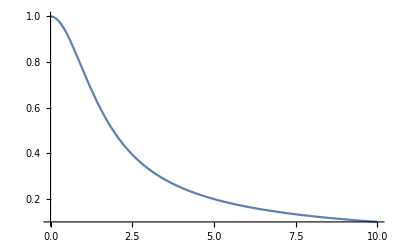

```mathematica
Plot[Tanh[x]/x,{x,0,10}]
```

### D_s(T) plot: fix U_1

```mathematica
(*m=0.1*)
```

```mathematica
u1=0.4977;J=1;m=0.1;
delta0=0.01;
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,41}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.78125,Null}

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data01=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=0.01*)
```

```mathematica
u1=0.4977;J=1;m=0.01;
delta0=0.01;
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,49}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.921875,Null}

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data001=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
(*m=0*)
```

```mathematica
u1=0.4977;J=1;m=0;
delta0=0.01;
templist=Table[0.0001 (ioft-1)+0.00001,{ioft,1,51}];
deltalist={};
newdelta=delta0;
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
secantu1t[newdelta];
newdelta=delta;
(*Print[newdelta];*)
AppendTo[deltalist,newdelta];
]//Timing
```

{0.984375,Null}

```mathematica
dsgeolist={};
dsconvlist={};
For[i=1,i<Length[templist]+1,i++,
temp=templist[[i]];
deltat=deltalist[[i]];
AppendTo[dsgeolist,dsgeo[J,m,deltat,temp]];
AppendTo[dsconvlist,dsconv[J,m,deltat,temp]];
]
data0=Table[{templist[[j]],dsgeolist[[j]]+dsconvlist[[j]]},{j,1,Length[templist]}];
```

```mathematica
data01first=Table[data01[[j]],{j,1,19}];
data01second=Table[data01[[j]],{j,20,41}];
data001first=Table[data001[[j]],{j,1,31}];
data001second=Table[data001[[j]],{j,32,49}];
data0first=Table[data0[[j]],{j,1,34}];
data0second=Table[data0[[j]],{j,35,Length[templist]}];
```

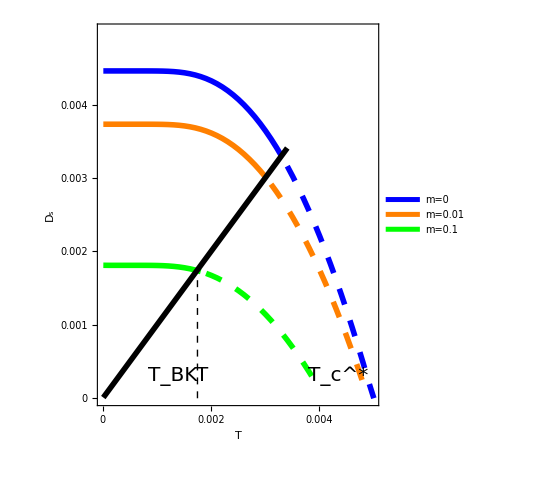

```mathematica
line=Table[{templist[[j]],templist[[j]]},{j,1,35}];
tbktniceplot2=ListPlot[{data0first,data001first,(*data003first,*)data01first,line,data0second,data001second,(*data003second,*)data01second},Joined->True,
PlotStyle->{{Thick,Blue,Thickness[0.01]},{Thick,Orange,Thickness[0.01]},{Thick,Green,Thickness[0.01]},(*{Thick,Red},*){Thick,Black,Thickness[0.01]},{Thick,Blue,Thickness[0.01],Dashing[{0.03,0.03}]},{Thick,Orange,Thickness[0.01],Dashing[{0.03,0.03}]},{Thick,Green,Thickness[0.01],Dashing[{0.03,0.03}]}(*,{Thick,Red,Dashed}*)},PlotRange->{{0,0.005},{0,0.005}},
LabelStyle->Directive[Black, 20],
Frame->True,FrameLabel->{Style["T",25],Style["D_s",25]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0,0.001,0.002,0.003,0.004},None},{{0,0.001,0.002,0.003,0.004,0.005},None}},
PlotLegends->Placed[{Style["m=0",20],Style["m=0.01",20],(*Style["m=0.032",20],*)Style["m=0.1",20]},{0.82,0.85}],
Epilog->{Text[Style["T_c^*",20],{0.00435,0.0003}],Dashed,Thick,Line[{{0.00175,0},{0.00175,0.00175}}],Text[Style["T_BKT",20],{0.0014,0.0003}]},
AspectRatio->1.2,ImageSize->400
]
```

```mathematica
Export["tbktnice2.pdf",tbktniceplot2]
```

tbktnice2.pdf

## a two dimensional secant method to determine T_BKT (treat Δ and T as two variables and the two equations are gap eq 1 and the BKT eq)

### DEFINITION (two equations): u1tceq, bkteq

u1tceq is already defined previously, but redefined here as gapu1! The arguments are [J,m, delta, temp]

```mathematica
gapu1[J_?NumericQ,m_?NumericQ,delta_?NumericQ,temp_?NumericQ]:=
u1 NIntegrate[(k/(2π))(((1-hzhat[J,m,k])/(4delta))Tanh[delta/(2temp)]+((1+hzhat[J,m,k])/(4Sqrt[edisp[J,m,k]^2+delta^2]))Tanh[Sqrt[edisp[J,m,k]^2+delta^2]/(2temp)]),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]-1
```

```mathematica
bkteq[J_?NumericQ,m_?NumericQ,delta_?NumericQ,temp_?NumericQ]:=
(π/8)(dsconv[J,m,delta,temp]+dsgeo[J,m,delta,temp])-temp
```

```mathematica
bkteqgeo[J_?NumericQ,m_?NumericQ,delta_?NumericQ,temp_?NumericQ]:=
(π/8)dsgeo[J,m,delta,temp]-temp
```

```mathematica
(*total SW*)
```

```mathematica
tbktsecantstep[{delta0_,temp0_},{delta1_,temp1_}]:=(
input0={delta0,temp0};
input1={delta1,temp1};
functionlist={gapu1,bkteq};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][J,m,changelist1[[1]],changelist1[[2]]]-functionlist[[i]][J,m,input1[[1]],input1[[2]]])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
inversetimes=inversejacob.Table[functionlist[[k]][J,m,input1[[1]],input1[[2]]],{k,1,2}];
alpha=1/(1+10Norm[inversetimes]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
tbktsecant[inputdelta_,inputtemp_,u1_,m_]:=(
alpha=0.1;
outputlist1={inputdelta,inputtemp};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.99,tbktsecantstep[outputlist0,outputlist1];];
deltafinal=outputlist1[[1]];
tempfinal=outputlist1[[2]];
)
```

```mathematica
(*if only count geo SW*)
```

```mathematica
tbktsecantstepgeo[{delta0_,temp0_},{delta1_,temp1_}]:=(
input0={delta0,temp0};
input1={delta1,temp1};
functionlist={gapu1,bkteqgeo};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][J,m,changelist1[[1]],changelist1[[2]]]-functionlist[[i]][J,m,input1[[1]],input1[[2]]])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
inversetimes=inversejacob.Table[functionlist[[k]][J,m,input1[[1]],input1[[2]]],{k,1,2}];
alpha=1/(1+10Norm[inversetimes]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
tbktsecantgeo[inputdelta_,inputtemp_,u1_,m_]:=(
alpha=0.1;
outputlist1={inputdelta,inputtemp};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.99,tbktsecantstepgeo[outputlist0,outputlist1];];
deltafinal=outputlist1[[1]];
tempfinal=outputlist1[[2]];
)
```

### T_BKT small Δ calculation

```mathematica
(*total SW calculation*)
```

```mathematica
J=1;m=0.1;
deltalist=Table[0.0005(idelta-1)+0.0001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001];
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data01total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{2.78125,Null}

```mathematica
J=1;m=0.032;
deltalist=Table[0.0005(idelta-1)+0.0001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001];
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data003total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{3.53125,Null}

```mathematica
J=1;m=0.01;
deltalist=Table[0.0005(idelta-1)+0.0001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001];
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data001total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{4.76563,Null}

```mathematica
J=1;m=0;
deltalist=Table[0.0005(idelta-1)+0.0001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001];
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data0total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{4.79688,Null}

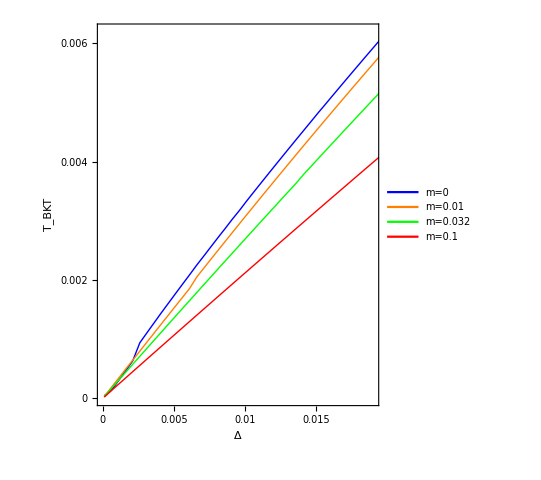

```mathematica
tbktsmalldelta=ListPlot[{data0total,data001total,data003total,data01total},
Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Red}},PlotRange->{{0,0.019},{0,0.0062}},
Frame->True,FrameLabel->{{"T_BKT",None},{"Δ",None}},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0,0.002,0.004,0.006},None},{{0,0.005,0.01,0.015},None}},
LabelStyle->Directive[Black, 23],
PlotLegends->Placed[{Style["m=0",20],Style["m=0.01",20],Style["m=0.032",20],Style["m=0.1",20]},{0.8,0.22}],
(*Epilog->{Text[Style["T_c^*",20],{0.00435,0.0003}],Dashed,Line[{{0.0021,0},{0.0021,0.0021}}],Text[Style["T_BKT",20],{0.0017,0.0003}]},*)
ImageSize->400,AspectRatio->1.2]
```

```mathematica
Export["tbktsmall.pdf",tbktsmalldelta]
```

tbktsmall.pdf

### T_BKT large Δ calculation (*)

```mathematica
(*total SW*)
```

```mathematica
J=1;m=0;
deltalist=Table[0.05(idelta-1)+0.001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=(π/8)(dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001]);
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data0total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{2.59375,Null}

```mathematica
J=1;m=0.1;
deltalist=Table[0.05(idelta-1)+0.001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=(π/8)(dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001]);
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data02total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{3.26563,Null}

```mathematica
J=1;m=0.5;
deltalist=Table[0.05(idelta-1)+0.001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=(π/8)(dsconv[J,m,deltainitial,0.0001]+dsgeo[J,m,deltainitial,0.0001]);
tbktsecant[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data1total=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{3.29688,Null}

```mathematica
(*geo SW only*)
```

```mathematica
J=1;m=0;
deltalist=Table[0.05(idelta-1)+0.001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=(π/8)dsgeo[J,m,deltainitial,0.0001];
tbktsecantgeo[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data0geo=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{1.79688,Null}

```mathematica
J=1;m=0.1;
deltalist=Table[0.05(idelta-1)+0.001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=(π/8)dsgeo[J,m,deltainitial,0.0001];
tbktsecantgeo[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data02geo=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{2.21875,Null}

```mathematica
J=1;m=0.5;
deltalist=Table[0.05(idelta-1)+0.001,{idelta,1,40}];
u1list={};
tbktlist={};
For[idelta=1,idelta<Length[deltalist]+1,idelta++,
deltainitial=deltalist[[idelta]];
u1=1/u1integralt0[J,m,deltainitial];
tempinitial=(π/8)dsgeo[J,m,deltainitial,0.0001];
tbktsecantgeo[deltainitial,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data1geo=Table[{deltalist[[j]],tbktlist[[j]]},{j,1,Length[deltalist]}];
```

{2.10938,Null}

```mathematica
(*PlotMarkers->{{m1,0.018},{m2,0.018},{m3,0.018}}*)
```

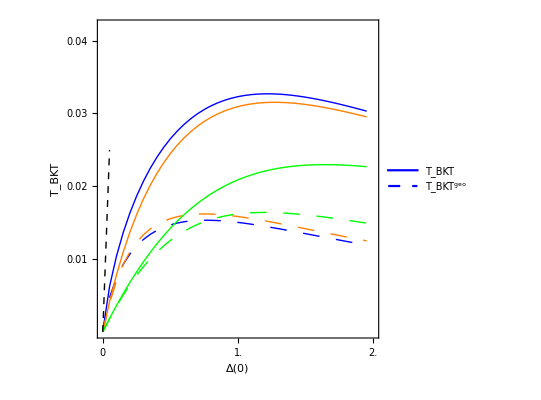

```mathematica
tbktvsdelta=ListPlot[{data0total,data0geo,data02total,data02geo,data1total,data1geo},
Joined->True,
PlotStyle->{{Thick,Blue},{Thick,Blue,Dashing[{0.03,0.03}]},{Thick,Orange},{Thick,Orange,Dashing[{0.03,0.03}]},{Thick,Green},{Thick,Green,Dashing[{0.03,0.03}]}},PlotRange->{{0,2},{0,0.042}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["Δ(0)",28],Style["T_BKT",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.01,0.02,0.03,0.04},None},{{0,0.5,1.0,1.5,2.0,2.5},None}},
LabelStyle->Directive[Black, 25],
PlotLegends->Placed[LineLegend[{Style["T_BKT",25],Style["T_BKT^geo",25]},LegendLayout->"Row"],{0.5,0.9}],
Epilog->{Dashed,Thick,Line[{{0,0},{0.05,0.025}}]},
AspectRatio->1,ImageSize->400]
```

```mathematica
Export["tbktvsdeltaplot.pdf",tbktvsdelta]
```

tbktvsdeltaplot.pdf

```mathematica
(*{m1,m2,m3}=Graphics/@{{Blue,Disk[{0,0},0.1]},{Orange,Polygon[{{0,0},{0.5,Sqrt[3]/2},{1,0}}]},{Green,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]}}*)
```

### T_BKT vs m calculation(*)

```mathematica
(*total SW*)
```

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,101}];
u1list={};
tbktlist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
tempinitial=(π/8)(dsconv[J,m,delta,0.0001]+dsgeo[J,m,delta,0.0001]);
tbktsecant[delta,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data01total=Table[{mlist[[j]]/delta,2tbktlist[[j]]/delta},{j,1,Length[mlist]}];
```

{7.59375,Null}

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,101}];
u1list={};
tbktlist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
tempinitial=(π/8)dsgeo[J,m,delta,0.0001];
tbktsecantgeo[delta,tempinitial,u1,m];
AppendTo[u1list,u1];
AppendTo[tbktlist,tempfinal];
]//Timing
data01geo=Table[{mlist[[j]]/delta,2tbktlist[[j]]/delta},{j,1,Length[mlist]}];
```

{5.15625,Null}

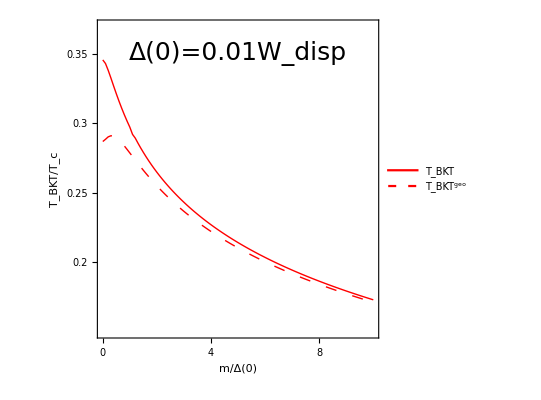

```mathematica
tbktvsm=ListPlot[{data01total,data01geo},
Joined->True,
PlotStyle->{{Thick,Red},{Thick,Red,Dashing[{0.02,0.03}]}},PlotRange->{{0,10},{0.15,0.37}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ(0)",28],Style["T_BKT/T_c",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.25,0.3,0.35},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[Black, 25],
PlotLegends->Placed[LineLegend[{Style["T_BKT",25],Style["T_BKT^geo",25]}],{0.75,0.6}],
Epilog->{Text[Style["Δ(0)=0.01W_disp",25],{5,0.35}]},
AspectRatio->1,ImageSize->400]
```

```mathematica
Export["tbktvsmplot.pdf",tbktvsm]
```

tbktvsmplot.pdf

### Ds vs m calculation(* Delta=0.01)

```mathematica
(*total SW*)
```

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,101}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dstotvalue=dsconv[J,m,delta,0.00001]+dsgeo[J,m,delta,0.0001];
AppendTo[u1list,u1];
AppendTo[dslist,dstotvalue];
]//Timing
data01total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.796875,Null}

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,101}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsgeovalue=dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsgeovalue];
]//Timing
data01geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.5625,Null}

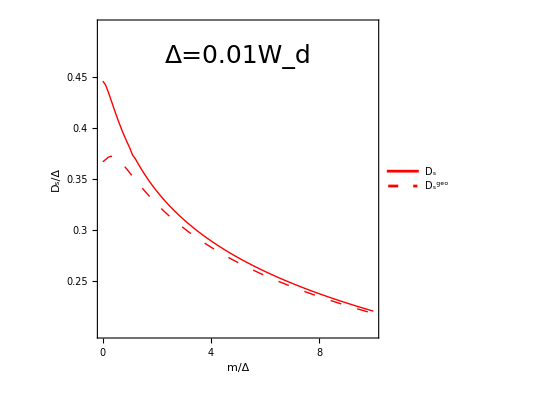

```mathematica
dsvsm=ListPlot[{data01total,data01geo},
Joined->True,
PlotStyle->{{Thick,Red},{Thick,Red,Dashing[{0.02,0.03}]}},PlotRange->{{0,10},{0.2,0.5}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",28],Style["D_s/Δ",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.25,0.3,0.35,0.4,0.45},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[Black, 25],
PlotLegends->Placed[LineLegend[{Style["D_s",25],Style["D_s^geo",25]}],{0.75,0.65}],
Epilog->{Text[Style["Δ=0.01W_d",25],{5,0.47}]},
AspectRatio->1,ImageSize->400]
```

```mathematica
Export["dsvsmplot.pdf",dsvsm]
```

tbktvsmplot.pdf

```mathematica
N[Log[10]]
```

2.30259

### Ds vs m calculation(* Delta=0.01 and 0.1 combined, J=1)

{0.46875,Null}

{0.234375,Null}

{0.5,Null}

```mathematica
(*SW total, 0.01*)
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dstotvalue=dsconv[J,m,delta,0.00001]+dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dstotvalue];
]//Timing
data001total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.296875,Null}

```mathematica
(*SW geo, 0.01*)
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsgeovalue=dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsgeovalue];
]//Timing
data001geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.25,Null}

```mathematica
(*SW conv, 0.01*)
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsconvvalue=dsconv[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsconvvalue];
]//Timing
data001conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.171875,Null}

```mathematica
(*SW total, 0.1*)
J=1;delta=0.1;
mlist=Table[0.01(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dstotvalue=dsconv[J,m,delta,0.00001]+dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dstotvalue];
]//Timing
data01total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.3125,Null}

```mathematica
(*SW geo, 0.1*)
J=1;delta=0.1;
mlist=Table[0.01(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsgeovalue=dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsgeovalue];
]//Timing
data01geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.046875,Null}

```mathematica
(*SW conv, 0.1*)
J=1;delta=0.1;
mlist=Table[0.01(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsconvvalue=dsconv[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsconvvalue];
]//Timing
data01conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.125,Null}

```mathematica
dsvsm=ListPlot[{data001total,data001geo,data001conv,data01total,data01geo,data01conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed},{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}},PlotRange->{{0,5},{0,0.46}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->600]
```

-Graphics-

```mathematica
Export["dsvsmplot.pdf",dsvsm]
```

dsvsmplot.pdf

### Ds vs m calculation(Delta=0.01 and 0.1 combined, J=2)

{0.46875,Null}

{0.234375,Null}

{0.5,Null}

```mathematica
(*SW total, 0.01*)
J=2;delta=0.01;
mlist=Table[0.001(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dstotvalue=dsconv[J,m,delta,0.00001]+dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dstotvalue];
]//Timing
data001total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.53125,Null}

```mathematica
(*SW geo, 0.01*)
J=2;delta=0.01;
mlist=Table[0.001(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsgeovalue=dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsgeovalue];
]//Timing
data001geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.3125,Null}

```mathematica
(*SW conv, 0.01*)
J=2;delta=0.01;
mlist=Table[0.001(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsconvvalue=dsconv[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsconvvalue];
]//Timing
data001conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.234375,Null}

```mathematica
(*SW total, 0.1*)
J=2;delta=0.1;
mlist=Table[0.01(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dstotvalue=dsconv[J,m,delta,0.00001]+dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dstotvalue];
]//Timing
data01total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.578125,Null}

```mathematica
(*SW geo, 0.1*)
J=2;delta=0.1;
mlist=Table[0.01(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsgeovalue=dsgeo[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsgeovalue];
]//Timing
data01geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.421875,Null}

```mathematica
(*SW conv, 0.1*)
J=2;delta=0.1;
mlist=Table[0.01(im-1),{im,1,51}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsconvvalue=dsconv[J,m,delta,0.00001];
AppendTo[u1list,u1];
AppendTo[dslist,dsconvvalue];
]//Timing
data01conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.375,Null}

```mathematica
dsvsm=ListPlot[{data001total,data001geo,data001conv,data01total,data01geo,data01conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed},{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}},PlotRange->{{0,5},{0,1}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->600]
```

-Graphics-

```mathematica
Export["dsvsmplot.pdf",dsvsm]
```

tbktvsmplot.pdf

```mathematica
1/1.764
```

0.566893

### Ds vs m calculation(* using dszerot function, nothing changed)

```mathematica
(*total SW*)
```

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,101}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dstotvalue=dsconvzerot[J,m,delta]+dsgeozerot[J,m,delta];
AppendTo[u1list,u1];
AppendTo[dslist,dstotvalue];
]//Timing
data01total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.625,Null}

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(im-1),{im,1,101}];
u1list={};
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
u1=1/u1integralt0[J,m,delta];
dsgeovalue=dsgeozerot[J,m,delta];
AppendTo[u1list,u1];
AppendTo[dslist,dsgeovalue];
]//Timing
data01geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.484375,Null}

```mathematica
dsvsm=ListPlot[{data01total,data01geo},
Joined->True,
PlotStyle->{{Thick,Red},{Thick,Red,Dashing[{0.02,0.03}]}},PlotRange->{{0,10},{0.2,0.5}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",28],Style["D_s/Δ",28]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.25,0.3,0.35,0.4,0.45},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[Black, 25],
PlotLegends->Placed[LineLegend[{Style["D_s",25],Style["D_s^geo",25]}],{0.75,0.65}],
Epilog->{Text[Style["Δ=0.01W_d",25],{5,0.47}]},
AspectRatio->1,ImageSize->400]
```

-Graphics-

```mathematica
Export["dsvsmplot.pdf",dsvsm]
```

tbktvsmplot.pdf

## numerical D_s^conv and D_s^geo

### calculation, delta up to 5

```mathematica
J=1;m=0;
swconvlist={};
swgeolist={};
deltalist=Table[0.1i,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data0geo=Table[{0.1i,swgeolist[[i]]},{i,1,Length@swgeolist}];
data0conv=Table[{0.1i,swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.1;
swconvlist={};
swgeolist={};
deltalist=Table[0.1i,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data01geo=Table[{0.1i,swgeolist[[i]]},{i,1,Length@swgeolist}];
data01conv=Table[{0.1i,swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.5;
swconvlist={};
swgeolist={};
deltalist=Table[0.1i,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data05geo=Table[{0.1i,swgeolist[[i]]},{i,1,Length@swgeolist}];
data05conv=Table[{0.1i,swconvlist[[i]]},{i,1,Length@swconvlist}];
```

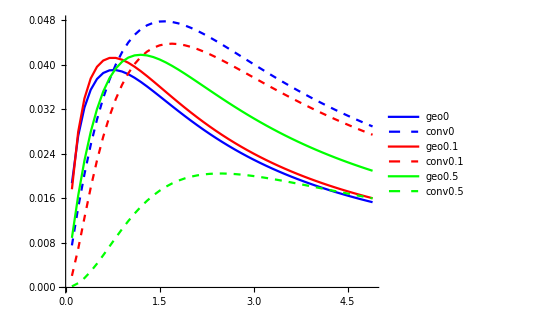

```mathematica
ListPlot[{data0geo,data0conv,data01geo,data01conv,data05geo,data05conv},Joined->True,PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed},Green,{Green,Dashed}},PlotLegends->{"geo0","conv0","geo0.1","conv0.1","geo0.5","conv0.5"},AspectRatio->0.8]
```

Looks exactly the same as analytical calculation!

### calculation, delta up to 0.1

```mathematica
J=1;m=0;
swconvlist={};
swgeolist={};
deltalist=Table[0.01i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data0geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data0conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.1;
swconvlist={};
swgeolist={};
deltalist=Table[0.01i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data01geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data01conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.5;
swconvlist={};
swgeolist={};
deltalist=Table[0.01i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data05geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data05conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

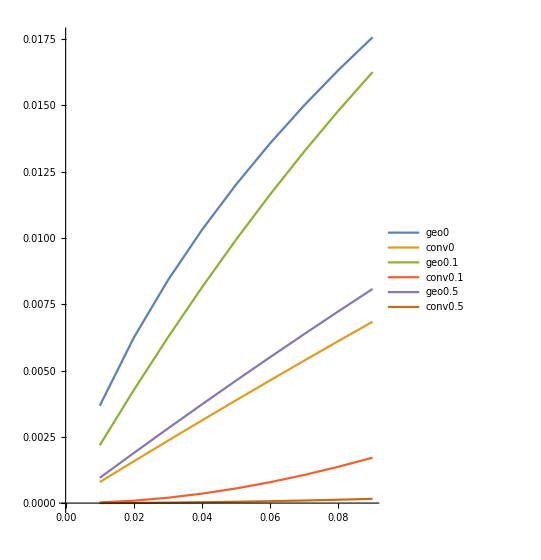

```mathematica
ListPlot[{data0geo,data0conv,data01geo,data01conv,data05geo,data05conv},Joined->True,PlotLegends->{"geo0","conv0","geo0.1","conv0.1","geo0.5","conv0.5"},AspectRatio->1.4]
```

Looks exactly the same as analytical calculation!

### calculation, delta up to 0.01

```mathematica
J=1;m=0;
swconvlist={};
swgeolist={};
deltalist=Table[0.001i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data0geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data0conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.1;
swconvlist={};
swgeolist={};
deltalist=Table[0.001i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data01geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data01conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.5;
swconvlist={};
swgeolist={};
deltalist=Table[0.001i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data05geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data05conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

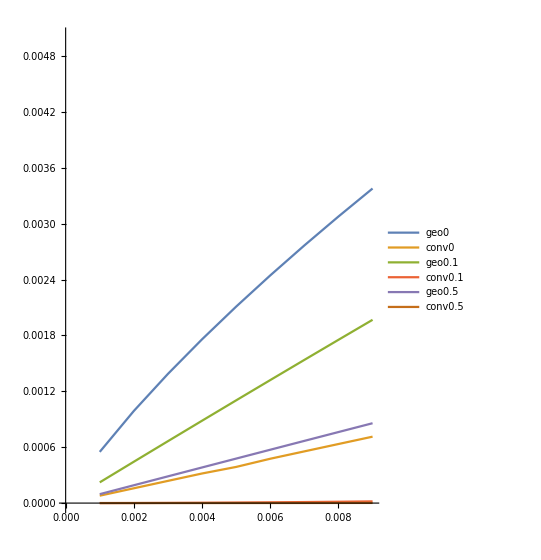

```mathematica
ListPlot[{data0geo,data0conv,data01geo,data01conv,data05geo,data05conv},Joined->True,
PlotRange->{0,0.005},PlotLegends->{"geo0","conv0","geo0.1","conv0.1","geo0.5","conv0.5"},AspectRatio->1.4]
```

Looks exactly the same as analytical calculation!

## singular band touching (flat band dispersive)

### def: two dispersive bands for singular touching

```mathematica
eup[J_,m_,k_]:=Sqrt[k^(2J)+m^2]+k^J
```

```mathematica
edown[J_,m_,k_]:=-Sqrt[k^(2J)+m^2]+k^J
```

```mathematica
(*the x direction has been averaged*)
vupsquare[J_,m_,k_]:=((J/Sqrt[m^2+k^(2J)])(1/√2)k^(2J-1)+J k^(J-1)(1/√2))^2
```

```mathematica
(*the x direction has been averaged*)
vdownsquare[J_,m_,k_]:=(-(J/Sqrt[m^2+k^(2J)])(1/√2)k^(2J-1)+J k^(J-1)(1/√2))^2
```

```mathematica
quasiup[J_,m_,k_,deltat_]:=Sqrt[eup[J,m,k]^2+deltat^2]
```

```mathematica
quasidown[J_,m_,k_,deltat_]:=Sqrt[edown[J,m,k]^2+deltat^2]
```

```mathematica
(*total Ds integral*)
dsconvsingular[J_?NumericQ,m_?NumericQ,deltat_?NumericQ]:=NIntegrate[(k/(2π))(deltat^2/quasiup[J,m,k,deltat]^3)vupsquare[J,m,k]+(k/(2π))(deltat^2/quasidown[J,m,k,deltat]^3)vdownsquare[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
dsgeosingular[J_?NumericQ,m_?NumericQ,deltat_?NumericQ]:=NIntegrate[(k/(2π))(4deltat^2/quasiup[J,m,k,deltat]+4deltat^2/quasidown[J,m,k,deltat]-(8deltat^2/(quasiup[J,m,k,deltat]+quasidown[J,m,k,deltat]))(1+(eup[J,m,k]edown[J,m,k]+deltat^2)/(quasiup[J,m,k,deltat]quasidown[J,m,k,deltat])))gvxx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### calculation, delta up to 5

```mathematica
J=4;m=0;
swconvlist={};
swgeolist={};
deltalist=Table[0.01(i-1)+0.001,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconvsingular[J,m,deltalist[[i]]];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeosingular[J,m,deltalist[[i]]];
AppendTo[swgeolist,swgeovalue];
]
data0geo=Table[{0.01(i-1)+0.001,swgeolist[[i]]},{i,1,Length@swgeolist}];
data0conv=Table[{0.01(i-1)+0.001,swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=4;m=0.1;
swconvlist={};
swgeolist={};
deltalist=Table[0.01(i-1)+0.001,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconvsingular[J,m,deltalist[[i]]];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeosingular[J,m,deltalist[[i]]];
AppendTo[swgeolist,swgeovalue];
]
data01geo=Table[{0.01(i-1)+0.001,swgeolist[[i]]},{i,1,Length@swgeolist}];
data01conv=Table[{0.01(i-1)+0.001,swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=4;m=0.5;
swconvlist={};
swgeolist={};
deltalist=Table[0.01(i-1)+0.001,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconvsingular[J,m,deltalist[[i]]];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeosingular[J,m,deltalist[[i]]];
AppendTo[swgeolist,swgeovalue];
]
data05geo=Table[{0.01(i-1)+0.001,swgeolist[[i]]},{i,1,Length@swgeolist}];
data05conv=Table[{0.01(i-1)+0.001,swconvlist[[i]]},{i,1,Length@swconvlist}];
```

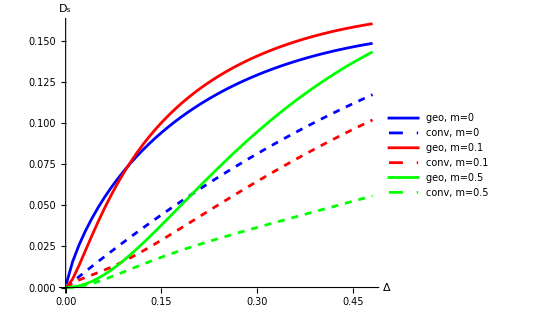

```mathematica
singularcase=ListPlot[{data0geo,data0conv,data01geo,data01conv,data05geo,data05conv},Joined->True,PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed},Green,{Green,Dashed}},PlotLegends->{"geo, m=0","conv, m=0","geo, m=0.1","conv, m=0.1","geo, m=0.5","conv, m=0.5"},
AxesLabel->{"Δ","D_s"},LabelStyle->{Black,20},
AspectRatio->0.8]
```

```mathematica
Export["singular.pdf",singularcase]
```

singular.pdf

## numerical compute D_s/(D_s^geo)_flat

```mathematica
dsgeoflat[J_?NumericQ,m_?NumericQ,deltat_?NumericQ,temp_?NumericQ]:=NIntegrate[(k/(2π))4deltat^2(Tanh[deltat/(2temp)]/deltat)gvxx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### calculation, delta up to 5

```mathematica
J=1;m=0.02;
swtotlist={};
swgeoflatlist={};
deltalist=Table[0.01i,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swtotvalue=dsconv[J,m,deltalist[[i]],0.0001]+dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swtotlist,swtotvalue];
swgeoflatvalue=dsgeoflat[J,m,deltalist[[i]],0.0001];
AppendTo[swgeoflatlist,swgeoflatvalue];
]
ratio002=Table[{0.01i,swtotlist[[i]]/swgeoflatlist[[i]]},{i,1,Length@swtotlist}];
```

```mathematica
J=1;m=0.1;
swtotlist={};
swgeoflatlist={};
deltalist=Table[0.01i,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swtotvalue=dsconv[J,m,deltalist[[i]],0.0001]+dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swtotlist,swtotvalue];
swgeoflatvalue=dsgeoflat[J,m,deltalist[[i]],0.0001];
AppendTo[swgeoflatlist,swgeoflatvalue];
]
ratio01=Table[{0.01i,swtotlist[[i]]/swgeoflatlist[[i]]},{i,1,Length@swtotlist}];
```

```mathematica
J=1;m=0.5;
swtotlist={};
swgeoflatlist={};
deltalist=Table[0.01i,{i,1,50}];
For[i=1,i<Length[deltalist],i++,
swtotvalue=dsconv[J,m,deltalist[[i]],0.0001]+dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swtotlist,swtotvalue];
swgeoflatvalue=dsgeoflat[J,m,deltalist[[i]],0.0001];
AppendTo[swgeoflatlist,swgeoflatvalue];
]
ratio05=Table[{0.01i,swtotlist[[i]]/swgeoflatlist[[i]]},{i,1,Length@swtotlist}];
```

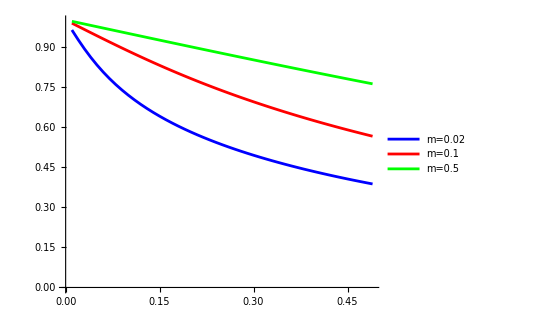

```mathematica
ListPlot[{ratio002,ratio01,ratio05},Joined->True,PlotStyle->{Blue,Red,Green},PlotLegends->{"m=0.02","m=0.1","m=0.5"},AspectRatio->0.8]
```

### calculation, delta up to 0.1

```mathematica
J=1;m=0;
swconvlist={};
swgeolist={};
deltalist=Table[0.01i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data0geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data0conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.1;
swconvlist={};
swgeolist={};
deltalist=Table[0.01i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data01geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data01conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.5;
swconvlist={};
swgeolist={};
deltalist=Table[0.01i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data05geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data05conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
ListPlot[{data0geo,data0conv,data01geo,data01conv,data05geo,data05conv},Joined->True,PlotLegends->{"geo0","conv0","geo0.1","conv0.1","geo0.5","conv0.5"},AspectRatio->1.4]
```

-Graphics-

Looks exactly the same as analytical calculation!

### calculation, delta up to 0.01

```mathematica
J=1;m=0;
swconvlist={};
swgeolist={};
deltalist=Table[0.001i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data0geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data0conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.1;
swconvlist={};
swgeolist={};
deltalist=Table[0.001i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data01geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data01conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
J=1;m=0.5;
swconvlist={};
swgeolist={};
deltalist=Table[0.001i,{i,1,10}];
For[i=1,i<Length[deltalist],i++,
swconvvalue=dsconv[J,m,deltalist[[i]],0.0001];
AppendTo[swconvlist,swconvvalue];
swgeovalue=dsgeo[J,m,deltalist[[i]],0.0001];
AppendTo[swgeolist,swgeovalue];
]
data05geo=Table[{deltalist[[i]],swgeolist[[i]]},{i,1,Length@swgeolist}];
data05conv=Table[{deltalist[[i]],swconvlist[[i]]},{i,1,Length@swconvlist}];
```

```mathematica
ListPlot[{data0geo,data0conv,data01geo,data01conv,data05geo,data05conv},Joined->True,
PlotRange->{0,0.005},PlotLegends->{"geo0","conv0","geo0.1","conv0.1","geo0.5","conv0.5"},AspectRatio->1.4]
```

-Graphics-

Looks exactly the same as analytical calculation!

## η vs integral quantum metric ***

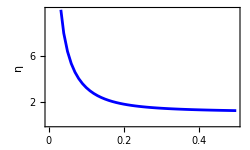

```mathematica
qmtable=Table[0.01i,{i,1,50}];
etalist={};
For[j=1,j<51,j++,qm=qmtable[[j]];
temp=NSolve[(π qm/2)(1-16t^4)==t&& t>0,t][[1]][[1]][[2]];
eta=0.5/temp;
AppendTo[etalist,eta];]
etaplot=ListPlot[Table[{qmtable[[i]],etalist[[i]]},{i,1,50}],Joined->True,PlotRange->{{0,0.5},{0,10}},
PlotStyle->Blue,
Frame->True,FrameLabel->{Style["ℳ",16],Style["η",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{2,4,6,8},None},{{0,0.1,0.2,0.3,0.4,0.5},None}},
LabelStyle->Directive[Black, 15],
AspectRatio->0.6,ImageSize->250]
```

```mathematica
Export["etaplot.pdf",etaplot]
```

etaplot.pdf

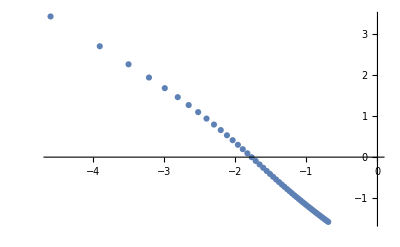

```mathematica
ListPlot[Table[{Log[qmtable[[i]]],Log[etalist[[i]]-1]},{i,1,50}]]
```

```mathematica
N[1/(4π)]
```

0.0795775

## band gap close schematic plot***

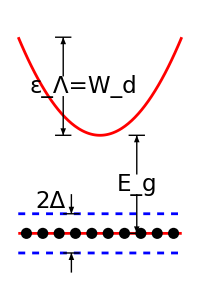

```mathematica
gap1=Plot[{0,10x^2+10,2,-2},{x,-1,1},
PlotRange->{{-1,1},{-4,21}},
PlotStyle->{Red,Red,Directive[Blue,Dashed],Directive[Blue,Dashed]},
Axes->False,
Epilog->{Black,Arrowheads[0.06],
(*1*)Line[{{-0.55,10},{-0.35,10}}],Line[{{-0.55,20},{-0.35,20}}],Arrow[{{-0.45,14},{-0.45,10}}],Arrow[{{-0.45,16},{-0.45,20}}],
Text[Style["ε_Λ=W_d",23],{-0.2,15}],
(*2*)Line[{{0.35,0},{0.55,0}}],Line[{{0.35,10},{0.55,10}}],Arrow[{{0.45,4},{0.45,0}}],Arrow[{{0.45,6},{0.45,10}}],
Text[Style["E_g",23],{0.45,5}],
(*3*)Line[{{-0.45,2},{-0.25,2}}],Line[{{-0.45,-2},{-0.25,-2}}],Arrow[{{-0.35,4},{-0.35,2}}],Arrow[{{-0.35,-4},{-0.35,-2}}],
Text[Style["2Δ",23,Italic],{-0.6,3.3}],
(*points*)PointSize[0.04],Table[Point[{0.2*i-1.1,0}],{i,1,10}]
},
AspectRatio->1.5,ImageSize->200]
```

```mathematica
Export["gap1.pdf",gap1]
```

gap1.pdf

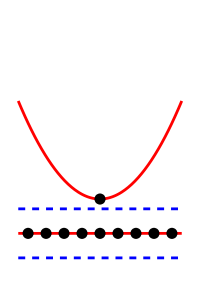

```mathematica
gap2=Plot[{0,10x^2+3.5,2.5,-2.5},{x,-1,1},
PlotRange->{{-1,1},{-4,21}},
PlotStyle->{Red,Red,Directive[Blue,Dashed],Directive[Blue,Dashed]},
Axes->False,
Epilog->{Black,(*points*)PointSize[0.04],Table[Point[{0.22*i-1.1,0}],{i,1,9}],Point[{0,3.5}]
},
AspectRatio->1.5,ImageSize->200]
```

```mathematica
Export["gap2.pdf",gap2]
```

gap2.pdf

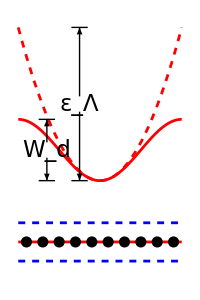

```mathematica
gap3=Plot[{0,-4Cos[π x]+12,2.5,-2.5,4*5x^2+8},{x,-1,1},
PlotRange->{{-1,1},{-4,28}},
PlotStyle->{Red,Red,Directive[Blue,Dashed],Directive[Blue,Dashed],Directive[Red,Dashed]},
Axes->False,
Epilog->{Black,Arrowheads[0.06],
(*1*)Line[{{-0.75,8},{-0.55,8}}],Line[{{-0.75,16},{-0.55,16}}],Arrow[{{-0.65,11},{-0.65,8}}],Arrow[{{-0.65,13},{-0.65,16}}],
Text[Style["W_d",23],{-0.65,12}],
(*2*)Line[{{-0.35,8},{-0.15,8}}],Line[{{-0.35,28},{-0.15,28}}],Arrow[{{-0.25,17},{-0.25,8}}],Arrow[{{-0.25,19},{-0.25,28}}],
Text[Style["ε_Λ",23],{-0.25,18}],
(*points*)PointSize[0.04],Table[Point[{0.2*i-1.1,0}],{i,1,10}]
},
AspectRatio->1.5,ImageSize->200]
```

```mathematica
Export["gap3.pdf",gap3]
```

gap3.pdf